```mathematica
CreateDialog@Manipulate[Module[{plots,fp},
(*fillingOption:=Which[And[showList2,fAxis===Filling->{1->{2}}],Filling->{1->{2}},And[!showList2,fAxis===Filling->{1->{2}}],Filling->Axis,And[showList2,fAxis=!=Filling->{1->{2}}],fAxis,And[!showList2,fAxis=!=Filling->{1->{2}}],fAxis];*)


(*fillingOption=Switch[And[showList2,fAxis===(Filling->{1->{2}})],True,(Filling->{1->{2}}),False,(Filling->Axis),And[showList2,fAxis=!=(Filling->{1->{2}})],True,fAxis,And[!showList2,fAxis=!=(Filling->{1->{2}})],True,fAxis,_,None];*)

(*fillingOption=If[And[showList2,fAxis===(Filling->{1->{2}})],(Filling->{1->{2}}),If[And[!showList2,fAxis===(Filling->{1->{2}})],(Filling->Axis),If[And[showList2,fAxis=!=(Filling->{1->{2}})],fAxis,If[And[!showList2,fAxis=!=(Filling->{1->{2}})],fAxis,If[fAxis==None,None]]]]];*)
(*CreateDialog@If[fip,Echo[plotss]];*)



plots={plottype[Tooltip@ReplaceAll[list0,{{αβ_,αg_}->{Axistype[αβ],αg}(*,

If[StringMatchQ[ToString[plottype],___~~"Log"~~___],{αβ_,0}->Nothing,Nothing]*)}],Joined->True,PlotRange->Full,GridLines->Full,ImageSize->ζ,Mesh->All,

MeshStyle->{If[pthame===(PlotTheme->"BlackBackground"),Yellow,Red]}(*,ColorFunction->If[pthame===(PlotTheme->"BlackBackground"),(ColorData["AlpineColors"][#2]&),Red]*),InterpolationOrder->SPoint,AspectRatio->650/(1.8 ζ),PlotStyle->{(*If[fbeak||fbeakbkg,Opacity[0.2],Nothing],*)PointSize[0.00008]},PlotRangeClipping->False,PlotRangePadding->None,Method->{"GridLinesInFront"->False},pthame,Filling->ReplaceAll[fAxis,"fAx"->None],Ticks->{Range[Length[list0]], Automatic},Epilog->Join@@{If[fbeak,{Green,PointSize[0.00008],Point/@list6 },Nothing],If[fbeakbkg,{LUVColor[.5,1,1],PointSize[0.00008],Point/@list7 },Nothing]}]};



If[(fAxis=="fAx")&&showList2,plots={plottype[Tooltip/@{First@list0,First@list2},Filling->{1->{{2},{Darker@LightBlue,Darker@Red}}},Joined->True,PlotRange->Full,GridLines->Full,ImageSize->ζ,Mesh->All,MeshStyle->{If[pthame===(PlotTheme->"BlackBackground"),Red,Darker[Red]]},InterpolationOrder->SPoint,AspectRatio->650/(1.8 ζ),PlotStyle->{PointSize[0.00005]},PlotRangeClipping->False,PlotRangePadding->None,Method->{"GridLinesInFront"->False},pthame,Ticks->{Range[Length[list0]], Automatic},Epilog->{If[fbeak,{Green,Point/@list6 },Nothing],If[fbeakbkg,{LUVColor[.5,1,1],Point/@list7 },Nothing]}]},ReplaceAll[fAxis,{"fAx"->None,fAxis->Axis}]];
(*If[MemberQ[H,f,2],c=First[Position[H,ToString[f]]⟦1⟧],CreateDialog[{TextCell["Not-Found"],ChoiceButtons[]}]];*)

If[showList1,AppendTo[plots,plottype[Tooltip@ReplaceAll[list1,{{αβ_,αg_}->{Axistype[αβ],αg},,}],PlotStyle->{(*If[fbeak||fbeakbkg,Opacity[0.2],Nothing],*)Red,PointSize[0.00015]},pthame,Ticks->{Range[Length[list0]], Automatic}]]];




If[showList2,AppendTo[plots,plottype[Tooltip@ReplaceAll[list2,{{αβ_,αg_}->{Axistype[αβ],αg},,}],Joined->True,PlotRange->Full,GridLines->Full,ImageSize->ζ,Mesh->All,AspectRatio->η,PlotStyle->{(*If[fbeak||fbeakbkg,Opacity[0.2],Nothing],*)PointSize[0.00005]},

MeshStyle->{If[pthame===(PlotTheme->"BlackBackground")(*,If[fbeak||fbeakbkg,Opacity[0.2],Nothing]*),Lighter[Red,0.4],Lighter[Darker[Red],0.4]]},InterpolationOrder->SPoint,PlotRangeClipping->False,PlotRangePadding->None,Method->{"GridLinesInFront"->False},pthame,Filling->ReplaceAll[fAxis,"fAx"->None],Ticks->{Range[Length[list0]], Automatic},

Epilog->Join@@{If[fbeak,{Green,Point/@list6 },Nothing],If[fbeakbkg,{LUVColor[.5,1,1],Point/@list7 },Nothing]}]]];




If[showList3,AppendTo[plots,plottype[Tooltip@ReplaceAll[list3,{{αβ_,αg_}->{Axistype[αβ],αg},}],MeshStyle->{(*If[fbeak||fbeakbkg,Opacity[0.2],Nothing],Lighter[Darker[Red],0.4],*)PointSize[0.0005]},pthame,Ticks->{Range[Length[list0]], Automatic},Epilog->Join@@{If[fbeak,{Green,Point/@list6 },Nothing],If[fbeakbkg,{LUVColor[.5,1,1],Point/@list7 },Nothing]}]]];



If[showList4,AppendTo[plots,plottype[Tooltip@ReplaceAll[list4,{{αβ_,αg_}->{Axistype[αβ],αg},,}],

PlotStyle->{(*If[fbeak||fbeakbkg,Opacity[0.2],Nothing],*)Purple,PointSize[0.0005]},pthame,Ticks->{Range[Length[list0]], Automatic},Epilog->Join@@{If[fbeak,{Green,Point/@list6 },Nothing],If[fbeakbkg,{LUVColor[.5,1,1],Point/@list7 },Nothing]}]]];




Apply[If[plotShow,Show,DynamicImage],plots]],







Style["Show Point",Bold,Medium],
Row[{
Column[{Control[{showList1,{False,True},Checkbox}],Control[{showList2,{False,True},Checkbox}],Control[{showList3,{False,True},Checkbox}],Control[{showList4,{False,True},Checkbox}]}],

Column[{Control[{{fbeak,False,"FindPeak"},{False,True},Checkbox}],Control[{{fbeakbkg,False,"FindPeakBKG"},{False,True},Checkbox}],Control[{{fsmoothb,False,"FindSmoothCurve"},{False,True},Checkbox}],Control[{{fsmoothbBKG,False,"FindSmoothCurveBKG"},{False,True},Checkbox}]}]}],

Delimiter,
Column[{Style["Coordnite",Bold,Medium],
Control[{plottype,{ListPlot->"Normal",ListLogPlot->"LogYaxis",ListLogLogPlot->"LogXYLog",ListLogLinearPlot->"LogXLog"},PopupMenu}]}],

Delimiter,
Column[{Style["x Axis Type",Bold,Medium],
Control[{Axistype,{fchtoene[fchanll[#]]&->"Chnall",fchanll->"Energy(kev)"},PopupMenu}]}]



,Column[{Style["plotShow",Bold,Medium],
Control[{plotShow,{True->"Show",False->"DynamicImage"},PopupMenu}]}]
,
Delimiter,
Column[{Style["Zoom",Bold,Medium],
Control[{{ζ,1000,"Zoom"},700,150000,ControlType -> Slider,ImageSize->110,Appearance->{Large,"DownArrow"}}],Dynamic[ζ],Row[{Control[{{f,"Am-241","f"},ControlType->InputField,ImageSize->{120,20}}]}]}]
,(*Control[{fip,{False,True},ControlType->Setter}]*)Button["Find",],
Delimiter,

Row[{
Column[{Style["PlotTheme",Bold,Medium],Control[],

Style["StylePoint",Bold,Medium]
,
Control[{{SPoint,1,""},{1->"Smooth",0->"Square",2->"FullSmooth"},PopupMenu}]}],


Control[{{fAxis,None,""},{None->"None",Delimiter,Axis->"FillingAxis",Delimiter,Top->"FillingTop",Delimiter,"fAx"->"Between",Delimiter},ControlType->RadioButtonBar,Appearance->"Vertical",Labeled->None}]

}]



(*,

Column[{Style["Ascpect",Bold,Medium],
Control[{{η,300/700,"Ascpect"},300/5000,300/170000,Slider}],Dynamic[η]}]*)
,
ControlPlacement->Left
,
ControlType->Setter
,
ControllerLinking->Full
,
Initialization:>(
list0=DeleteCases[,{_,0},2];
list1=DeleteCases[bb3,{_,0},2];
list2=DeleteCases[,{_,0},2];
list3=DeleteCases[γ2,{_,0}];
list4=DeleteCases[bb3kg,{_,0}];
list5=H;list6=Flatten[ROI2/@β2[[;;,1]],2];list7=Block[{x=xxbkg,γ2=γ2kg},Flatten[ROI2/@β2kg[[;;,1]],2]];
el=k1/.(Table[If[!Or@@eFil[k1⟦i⟧],k1⟦i⟧->Nothing],{i,Length[k1]}]/.Null->Nothing);),ContentSize->{850,400},Deployed->True,AppearanceElements->None]
```

ikcx9_shm103FrontEndObject[LinkObject["ikcx9_shm", 3, 1]]103103

```mathematica
bb3
```

{{175,4843}→Am-241,{547,1274}→U-235,{600,358}→U-235,{710,1676}→Pb-214,{867,3160}→Pb-214,{867,3160}→Xe-139,{1033,5348}→Pb-214,{1788,3583}→Bi-214,{1941,2383}→Cs-137,{2306,91}→Pb-214,{2334,39}→Cs-134,{3288,628}→Bi-214,{3633,226}→Bi-214,{5180,434}→Bi-214,{6473,91}→Bi-214}

```mathematica
xxbkg
```

{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,1},{10,0},{11,2},{12,4},{13,9},{14,7},{15,4834},{16,15574},{17,18529},{18,17192},{19,13159},8154,{8174,2},{8175,4},{8176,2},{8177,7},{8178,4},{8179,5},{8180,7},{8181,4},{8182,3},{8183,2},{8184,6},{8185,2},{8186,2},{8187,3},{8188,2},{8189,3},{8190,3},{8191,11},{8192,4}}
 |  |  |  |

```mathematica
u
```

u

```mathematica
MatchQ[{175,4843}->"Am-241",{a_,b_}->cr_]
```

True

```mathematica
list1/.({u_,au_}->bu_):>Callout[{u,au},bu]
```

{Callout[{175,4843},Am-241],Callout[{547,1274},U-235],Callout[{600,358},U-235],Callout[{710,1676},Pb-214],Callout[{867,3160},Pb-214],Callout[{867,3160},Xe-139],Callout[{1033,5348},Pb-214],Callout[{1788,3583},Bi-214],Callout[{1941,2383},Cs-137],Callout[{2306,91},Pb-214],Callout[{2334,39},Cs-134],Callout[{3288,628},Bi-214],Callout[{3633,226},Bi-214],Callout[{5180,434},Bi-214],Callout[{6473,91},Bi-214]}

```mathematica
list1[[;;,1]]
```

{{175,4843},{547,1274},{600,358},{710,1676},{867,3160},{867,3160},{1033,5348},{1788,3583},{1941,2383},{2306,91},{2334,39},{3288,628},{3633,226},{5180,434},{6473,91}}

```mathematica
ListPlot[list1/.({u_,au_}->bu_):>Callout[{u,au},bu,After,Appearance->"Corners",Background->LightGreen,LeaderSize->{15,-20 °,0},CalloutStyle->{Darker@Blue,LightGreen}]]
```

-Graphics-

```mathematica
Callout[Log[x]Sin[x],"label",Automatic,3,Appearance->"Corners",Background->LightGreen,LeaderSize->{50,30 °,0},CalloutStyle->{Darker@Blue,LightGreen}]
```

```mathematica
?ROI2
```

```mathematica
Block[{x=xxbkg,γ2=γ2kg},Flatten[ROI2/@β2kg[[;;,1]],2]]
```

{{138,491},{137,430},{136,397},{135,422},{134,421},{133,398},{138,491},{139,461},{140,428},{141,379},{142,379},{143,413},{144,375},{145,368},{146,402},{147,375},{157,476},{156,429},{155,378},{154,355},{153,391},{152,390},{151,427},{150,405},{149,358},{157,476},{158,468},{159,403},{160,396},{161,352},{162,411},{163,384},{164,407},{165,375},{186,503},{185,462},{184,457},{183,421},{182,408},{181,408},{180,408},{179,390},{178,370},{177,398},{176,387},{186,503},{187,459},{188,397},{189,422},{190,394},{191,382},{196,459},{195,440},{194,420},{193,393},{192,390},{191,382},{196,459},{197,423},{198,371},{214,674},{213,609},{212,469},{211,423},{214,674},{215,630},{216,520},{217,471},{221,969},{220,964},{219,690},{218,525},{217,471},{221,969},{222,734},{223,514},{224,429},{249,802},{248,675},{247,542},{246,453},{245,430},{244,427},{243,420},{242,417},{249,802},{250,747},{251,603},{252,528},{253,474},{254,443},{257,572},{256,527},{255,466},{254,443},{257,572},{258,520},{259,475},{260,410},{261,375},{272,817},{271,704},{270,482},{269,432},{268,377},{267,370},{266,444},{265,436},{264,437},{263,431},{262,383},{272,817},{273,772},{274,658},{275,474},{276,433},{277,405},{278,419},{279,412},{280,371},{411,553},{410,513},{409,529},{408,434},{411,553},{412,458},{413,507},{414,441},{415,490},{416,447},{422,561},{421,526},{420,530},{419,501},{418,458},{417,495},{416,447},{422,561},{423,506},{424,473},{425,504},{426,461},{427,436},{546,778},{545,737},{544,598},{543,530},{542,428},{541,479},{540,412},{539,455},{538,444},{537,395},{546,778},{547,595},{548,465},{549,459},{550,426},{551,441},{552,411},{577,489},{576,412},{575,439},{574,421},{573,439},{572,427},{571,404},{577,489},{578,409},{579,426},{580,419},{581,440},{582,436},{603,484},{602,429},{601,410},{600,458},{599,374},{603,484},{604,436},{605,451},{606,397},{607,367},{608,455},{609,450},{610,420},{611,416},{701,660},{700,645},{699,523},{698,432},{697,363},{696,406},{695,353},{694,405},{693,388},{701,660},{702,506},{703,408},{704,376},{705,405},{706,375},{866,437},{865,395},{864,338},{863,302},{862,319},{861,295},{866,437},{867,434},{868,385},{869,328},{870,323},{871,292},{872,333},{873,307},{874,277},{993,361},{992,292},{991,288},{990,252},{989,268},{988,252},{987,241},{993,361},{994,319},{995,267},{996,279},{997,247},{998,278},{999,231},{1033,536},{1032,472},{1031,427},{1030,311},{1029,271},{1028,249},{1027,234},{1026,281},{1025,228},{1024,248},{1023,229},{1033,536},{1034,404},{1035,332},{1036,282},{1037,233},{1038,213},{1499,940},{1498,828},{1497,806},{1496,601},{1495,470},{1494,338},{1493,313},{1492,224},{1491,216},{1490,191},{1489,170},{1499,940},{1500,910},{1501,801},{1502,688},{1503,514},{1504,408},{1505,327},{1506,247},{1507,193},{1508,200},{1509,200},{1711,241},{1710,225},{1709,208},{1708,180},{1707,140},{1706,131},{1711,241},{1712,208},{1713,215},{1714,170},{1715,143},{1716,133},{1717,159},{1718,132},{1788,362},{1787,356},{1786,293},{1785,226},{1784,174},{1783,165},{1782,134},{1781,173},{1780,136},{1779,108},{1788,362},{1789,275},{1790,263},{1791,175},{1792,159},{1793,147},{1794,124},{1795,144},{1796,99},{1859,163},{1858,132},{1857,131},{1856,123},{1855,114},{1859,163},{1860,127},{1861,116},{1862,149},{1863,133},{1864,127},{1865,117},{1866,132},{1867,129},{1868,123},{1874,157},{1873,128},{1872,102},{1871,127},{1870,108},{1869,146},{1868,123},{1874,157},{1875,129},{1876,109},{1877,140},{1878,125},{1879,118},{1880,146},{1881,138},{1882,134},{2134,153},{2133,136},{2132,118},{2131,130},{2130,127},{2129,120},{2128,95},{2127,126},{2126,120},{2125,115},{2134,153},{2135,113},{2355,149},{2354,121},{2353,125},{2352,123},{2351,109},{2350,102},{2355,149},{2356,114},{2357,116},{2358,101},{2359,101},{2672,196},{2671,165},{2670,123},{2669,104},{2668,107},{2667,83},{2672,196},{2673,187},{2674,178},{2675,168},{2676,131},{2677,121},{2678,116},{2679,88},{2680,101},{2681,95},{2682,93},{2830,121},{2829,96},{2828,94},{2827,81},{2826,78},{2825,73},{2830,121},{2831,109},{2832,108},{2833,88},{2834,103},{2835,94},{2836,87},{2837,101},{2838,93},{2839,92},{2842,161},{2841,135},{2840,99},{2839,92},{2842,161},{2843,149},{2844,146},{2845,130},{2846,119},{2847,97},{2848,87},{2849,84},{2850,85},{2851,81},{2852,78},{2858,110},{2857,72},{2858,110},{2859,99},{2860,82},{2861,83},{2862,74},{2905,105},{2904,68},{2905,105},{2906,83},{2907,87},{2908,66},{2909,86},{2910,82},{2937,120},{2936,86},{2935,83},{2934,95},{2933,92},{2932,82},{2931,74},{2930,96},{2929,84},{2928,72},{2937,120},{2938,114},{2939,117},{2940,99},{2941,72},{2942,72},{3152,103},{3151,87},{3150,62},{3149,82},{3148,76},{3147,66},{3146,58},{3152,103},{3153,75},{3289,163},{3288,148},{3287,138},{3286,140},{3285,131},{3284,106},{3283,95},{3282,71},{3281,65},{3289,163},{3290,115},{3291,81},{3292,85},{3293,63},{3294,76},{3295,41},{3324,99},{3323,69},{3322,73},{3321,65},{3320,75},{3319,70},{3324,99},{3325,68},{3326,82},{3327,72},{3335,95},{3334,71},{3333,80},{3332,74},{3331,66},{3330,55},{3329,81},{3328,74},{3327,72},{3335,95},{3336,63},{3399,99},{3398,75},{3397,77},{3396,61},{3395,85},{3394,60},{3399,99},{3400,73},{3401,61},{4044,93},{4043,75},{4042,70},{4041,49},{4040,67},{4039,48},{4038,54},{4037,49},{4036,45},{4044,93},{4045,62},{4046,66},{4047,50},{4048,36},{4131,72},{4130,45},{4129,58},{4128,50},{4127,42},{4126,33},{4125,50},{4124,41},{4123,35},{4122,34},{4131,72},{4132,65},{4133,63},{4134,59},{4135,45},{4136,44},{4137,42},{4138,52},{4139,39},{4140,45},{4141,40},{4287,986},{4286,848},{4285,690},{4284,440},{4283,264},{4282,137},{4281,78},{4280,52},{4279,51},{4278,47},{4277,37},{4287,986},{4288,842},{4289,723},{4290,522},{4291,309},{4292,158},{4293,101},{4294,59},{4295,32},{4296,29},{4297,29},{4430,62},{4429,50},{4428,59},{4427,32},{4426,36},{4425,31},{4430,62},{4431,46},{4432,41},{4433,33},{4434,23},{4435,51},{4436,39},{4437,25},{4438,40},{4439,34},{4661,64},{4660,56},{4659,56},{4658,41},{4657,32},{4656,27},{4655,26},{4654,21},{4653,25},{4652,23},{4651,34},{4661,64},{4662,48},{4663,44},{4664,47},{4665,36},{4666,29},{4667,33},{4668,33},{4742,40},{4741,21},{4740,25},{4739,16},{4738,28},{4737,28},{4736,25},{4735,22},{4742,40},{4743,22},{4744,27},{4745,19},{4757,57},{4756,49},{4755,40},{4754,27},{4753,34},{4752,25},{4751,16},{4750,25},{4749,23},{4748,23},{4757,57},{4758,41},{4759,33},{4760,33},{4761,26},{4762,25},{4763,21},{4786,53},{4785,38},{4784,42},{4783,29},{4782,19},{4786,53},{4787,46},{4788,34},{4789,35},{4790,32},{4791,26},{4792,30},{4793,27},{4794,20},{5079,51},{5078,42},{5077,47},{5076,36},{5075,42},{5074,34},{5073,34},{5072,32},{5071,26},{5070,25},{5069,18},{5079,51},{5080,28},{5081,35},{5082,26},{5083,17},{5084,16},{5085,15},{5086,32},{5087,18},{5088,14},{5092,33},{5091,20},{5090,18},{5089,21},{5088,14},{5092,33},{5093,18},{5094,16},{5095,21},{5096,19},{5179,187},{5178,150},{5177,117},{5176,85},{5175,66},{5174,49},{5173,32},{5172,25},{5171,20},{5170,17},{5169,15},{5179,187},{5180,164},{5181,143},{5182,121},{5183,78},{5184,44},{5185,34},{5186,28},{5187,11},{5296,36},{5295,18},{5294,17},{5296,36},{5297,16},{5298,24},{5299,13},{5423,50},{5422,41},{5421,30},{5420,24},{5419,24},{5418,17},{5417,17},{5416,21},{5415,19},{5414,22},{5413,18},{5423,50},{5424,38},{5425,31},{5426,31},{5427,29},{5428,21},{5429,29},{5430,20},{5431,15},{5432,26},{5433,14},{5457,33},{5456,32},{5455,16},{5457,33},{5458,12},{5459,20},{5460,19},{5461,14},{5462,20},{5463,17},{5464,13},{5526,31},{5525,21},{5524,21},{5523,16},{5522,20},{5521,20},{5520,16},{5519,21},{5518,12},{5526,31},{5527,21},{5528,11},{5529,10},{5530,16},{5531,12},{5608,35},{5607,25},{5606,14},{5605,23},{5604,18},{5603,15},{5602,19},{5601,16},{5600,14},{5608,35},{5609,23},{5610,16},{5611,23},{5612,19},{5613,25},{5614,20},{5615,18},{5616,15},{6471,73},{6470,51},{6469,57},{6468,51},{6467,44},{6466,24},{6465,21},{6464,23},{6463,13},{6462,10},{6471,73},{6472,65},{6473,61},{6474,49},{6475,40},{6476,24},{6477,29},{6478,20},{6479,17},{6480,12},{6481,20},{7677,406},{7676,344},{7675,315},{7674,229},{7673,155},{7672,90},{7671,54},{7670,38},{7669,23},{7668,20},{7667,12},{7677,406},{7678,398},{7679,374},{7680,345},{7681,227},{7682,187},{7683,120},{7684,72},{7685,34},{7686,19},{7687,9}}

```mathematica
Flatten[ROI2@(β2[[;;,1]][[1]]),1]
```

{{175,4843},{174,3088},{173,1349},{172,753},{171,554},{170,522},{169,523},{168,513},{167,505},{166,473},{165,439},{175,4843},{176,4358},{177,2066},{178,714},{179,411},{180,332},{181,346},{182,320},{183,320},{184,307}}

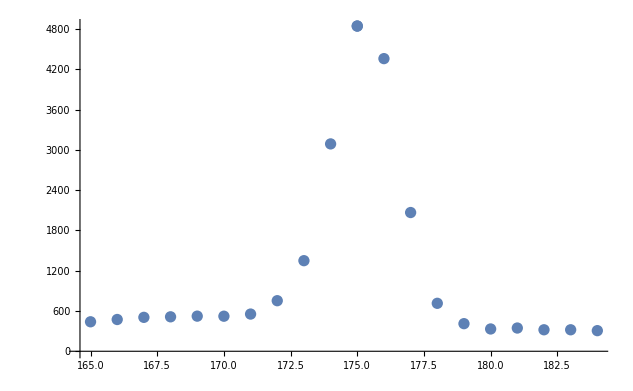

```mathematica
ListPlot[Tooltip[Flatten[ROI2@(β2[[;;,1]][[1]]),1]]]
```

```mathematica
Block[{x=xxbkg},Flatten[ROI2/@β2kg[[;;,1]],2]]
```

{{138,491},{137,430},{136,397},{135,422},{134,421},{133,398},{138,491},{139,461},{140,428},{141,379},{142,379},{143,413},{144,375},{145,368},{146,402},{147,375},{157,476},{156,429},{155,378},{154,355},{153,391},{152,390},{151,427},{150,405},{149,358},{157,476},{158,468},{159,403},{160,396},{161,352},{162,411},{163,384},{164,407},{165,375},{186,503},{185,462},{184,457},{183,421},{182,408},{181,408},{180,408},{179,390},{178,370},{177,398},{176,387},{186,503},{187,459},{188,397},{189,422},{190,394},{191,382},{196,459},{195,440},{194,420},{193,393},{192,390},{191,382},{196,459},{197,423},{198,371},{214,674},{213,609},{212,469},{211,423},{214,674},{215,630},{216,520},{217,471},{221,969},{220,964},{219,690},{218,525},{217,471},{221,969},{222,734},{223,514},{224,429},{249,802},{248,675},{247,542},{246,453},{245,430},{244,427},{243,420},{242,417},{249,802},{250,747},{251,603},{252,528},{253,474},{254,443},{257,572},{256,527},{255,466},{254,443},{257,572},{258,520},{259,475},{260,410},{261,375},{272,817},{271,704},{270,482},{269,432},{268,377},{267,370},{266,444},{265,436},{264,437},{263,431},{262,383},{272,817},{273,772},{274,658},{275,474},{276,433},{277,405},{278,419},{279,412},{280,371},{411,553},{410,513},{409,529},{408,434},{411,553},{412,458},{413,507},{414,441},{415,490},{416,447},{422,561},{421,526},{420,530},{419,501},{418,458},{417,495},{416,447},{422,561},{423,506},{424,473},{425,504},{426,461},{427,436},{546,778},{545,737},{544,598},{543,530},{542,428},{541,479},{540,412},{539,455},{538,444},{537,395},{546,778},{547,595},{548,465},{549,459},{550,426},{551,441},{552,411},{577,489},{576,412},{575,439},{574,421},{573,439},{572,427},{571,404},{577,489},{578,409},{579,426},{580,419},{581,440},{582,436},{603,484},{602,429},{601,410},{600,458},{599,374},{603,484},{604,436},{605,451},{606,397},{607,367},{608,455},{609,450},{610,420},{611,416},{701,660},{700,645},{699,523},{698,432},{697,363},{696,406},{695,353},{694,405},{693,388},{701,660},{702,506},{703,408},{704,376},{705,405},{706,375},{866,437},{865,395},{864,338},{863,302},{862,319},{861,295},{866,437},{867,434},{868,385},{869,328},{870,323},{871,292},{872,333},{873,307},{874,277},{993,361},{992,292},{991,288},{990,252},{989,268},{988,252},{987,241},{993,361},{994,319},{995,267},{996,279},{997,247},{998,278},{999,231},{1033,536},{1032,472},{1031,427},{1030,311},{1029,271},{1028,249},{1027,234},{1026,281},{1025,228},{1024,248},{1023,229},{1033,536},{1034,404},{1035,332},{1036,282},{1037,233},{1038,213},{1499,940},{1498,828},{1497,806},{1496,601},{1495,470},{1494,338},{1493,313},{1492,224},{1491,216},{1490,191},{1489,170},{1499,940},{1500,910},{1501,801},{1502,688},{1503,514},{1504,408},{1505,327},{1506,247},{1507,193},{1508,200},{1509,200},{1711,241},{1710,225},{1709,208},{1708,180},{1707,140},{1706,131},{1711,241},{1712,208},{1713,215},{1714,170},{1715,143},{1716,133},{1717,159},{1718,132},{1788,362},{1787,356},{1786,293},{1785,226},{1784,174},{1783,165},{1782,134},{1781,173},{1780,136},{1779,108},{1788,362},{1789,275},{1790,263},{1791,175},{1792,159},{1793,147},{1794,124},{1795,144},{1796,99},{1859,163},{1858,132},{1857,131},{1856,123},{1855,114},{1859,163},{1860,127},{1861,116},{1862,149},{1863,133},{1864,127},{1865,117},{1866,132},{1867,129},{1868,123},{1874,157},{1873,128},{1872,102},{1871,127},{1870,108},{1869,146},{1868,123},{1874,157},{1875,129},{1876,109},{1877,140},{1878,125},{1879,118},{1880,146},{1881,138},{1882,134},{2134,153},{2133,136},{2132,118},{2131,130},{2130,127},{2129,120},{2128,95},{2127,126},{2126,120},{2125,115},{2134,153},{2135,113},{2355,149},{2354,121},{2353,125},{2352,123},{2351,109},{2350,102},{2355,149},{2356,114},{2357,116},{2358,101},{2359,101},{2672,196},{2671,165},{2670,123},{2669,104},{2668,107},{2667,83},{2672,196},{2673,187},{2674,178},{2675,168},{2676,131},{2677,121},{2678,116},{2679,88},{2680,101},{2681,95},{2682,93},{2830,121},{2829,96},{2828,94},{2827,81},{2826,78},{2825,73},{2830,121},{2831,109},{2832,108},{2833,88},{2834,103},{2835,94},{2836,87},{2837,101},{2838,93},{2839,92},{2842,161},{2841,135},{2840,99},{2839,92},{2842,161},{2843,149},{2844,146},{2845,130},{2846,119},{2847,97},{2848,87},{2849,84},{2850,85},{2851,81},{2852,78},{2858,110},{2857,72},{2858,110},{2859,99},{2860,82},{2861,83},{2862,74},{2905,105},{2904,68},{2905,105},{2906,83},{2907,87},{2908,66},{2909,86},{2910,82},{2937,120},{2936,86},{2935,83},{2934,95},{2933,92},{2932,82},{2931,74},{2930,96},{2929,84},{2928,72},{2937,120},{2938,114},{2939,117},{2940,99},{2941,72},{2942,72},{3152,103},{3151,87},{3150,62},{3149,82},{3148,76},{3147,66},{3146,58},{3152,103},{3153,75},{3289,163},{3288,148},{3287,138},{3286,140},{3285,131},{3284,106},{3283,95},{3282,71},{3281,65},{3289,163},{3290,115},{3291,81},{3292,85},{3293,63},{3294,76},{3295,41},{3324,99},{3323,69},{3322,73},{3321,65},{3320,75},{3319,70},{3324,99},{3325,68},{3326,82},{3327,72},{3335,95},{3334,71},{3333,80},{3332,74},{3331,66},{3330,55},{3329,81},{3328,74},{3327,72},{3335,95},{3336,63},{3399,99},{3398,75},{3397,77},{3396,61},{3395,85},{3394,60},{3399,99},{3400,73},{3401,61},{4044,93},{4043,75},{4042,70},{4041,49},{4040,67},{4039,48},{4038,54},{4037,49},{4036,45},{4044,93},{4045,62},{4046,66},{4047,50},{4048,36},{4131,72},{4130,45},{4129,58},{4128,50},{4127,42},{4126,33},{4125,50},{4124,41},{4123,35},{4122,34},{4131,72},{4132,65},{4133,63},{4134,59},{4135,45},{4136,44},{4137,42},{4138,52},{4139,39},{4140,45},{4141,40},{4287,986},{4286,848},{4285,690},{4284,440},{4283,264},{4282,137},{4281,78},{4280,52},{4279,51},{4278,47},{4277,37},{4287,986},{4288,842},{4289,723},{4290,522},{4291,309},{4292,158},{4293,101},{4294,59},{4295,32},{4296,29},{4297,29},{4430,62},{4429,50},{4428,59},{4427,32},{4426,36},{4425,31},{4430,62},{4431,46},{4432,41},{4433,33},{4434,23},{4435,51},{4436,39},{4437,25},{4438,40},{4439,34},{4661,64},{4660,56},{4659,56},{4658,41},{4657,32},{4656,27},{4655,26},{4654,21},{4653,25},{4652,23},{4651,34},{4661,64},{4662,48},{4663,44},{4664,47},{4665,36},{4666,29},{4667,33},{4668,33},{4742,40},{4741,21},{4740,25},{4739,16},{4738,28},{4737,28},{4736,25},{4735,22},{4742,40},{4743,22},{4744,27},{4745,19},{4757,57},{4756,49},{4755,40},{4754,27},{4753,34},{4752,25},{4751,16},{4750,25},{4749,23},{4748,23},{4757,57},{4758,41},{4759,33},{4760,33},{4761,26},{4762,25},{4763,21},{4786,53},{4785,38},{4784,42},{4783,29},{4782,19},{4786,53},{4787,46},{4788,34},{4789,35},{4790,32},{4791,26},{4792,30},{4793,27},{4794,20},{5079,51},{5078,42},{5077,47},{5076,36},{5075,42},{5074,34},{5073,34},{5072,32},{5071,26},{5070,25},{5069,18},{5079,51},{5080,28},{5081,35},{5082,26},{5083,17},{5084,16},{5085,15},{5086,32},{5087,18},{5088,14},{5092,33},{5091,20},{5090,18},{5089,21},{5088,14},{5092,33},{5093,18},{5094,16},{5095,21},{5096,19},{5179,187},{5178,150},{5177,117},{5176,85},{5175,66},{5174,49},{5173,32},{5172,25},{5171,20},{5170,17},{5169,15},{5179,187},{5180,164},{5181,143},{5182,121},{5183,78},{5184,44},{5185,34},{5186,28},{5187,11},{5296,36},{5295,18},{5294,17},{5296,36},{5297,16},{5298,24},{5299,13},{5423,50},{5422,41},{5421,30},{5420,24},{5419,24},{5418,17},{5417,17},{5416,21},{5415,19},{5414,22},{5413,18},{5423,50},{5424,38},{5425,31},{5426,31},{5427,29},{5428,21},{5429,29},{5430,20},{5431,15},{5432,26},{5433,14},{5457,33},{5456,32},{5455,16},{5457,33},{5458,12},{5459,20},{5460,19},{5461,14},{5462,20},{5463,17},{5464,13},{5526,31},{5525,21},{5524,21},{5523,16},{5522,20},{5521,20},{5520,16},{5519,21},{5518,12},{5526,31},{5527,21},{5528,11},{5529,10},{5530,16},{5531,12},{5608,35},{5607,25},{5606,14},{5605,23},{5604,18},{5603,15},{5602,19},{5601,16},{5600,14},{5608,35},{5609,23},{5610,16},{5611,23},{5612,19},{5613,25},{5614,20},{5615,18},{5616,15},{6471,73},{6470,51},{6469,57},{6468,51},{6467,44},{6466,24},{6465,21},{6464,23},{6463,13},{6462,10},{6471,73},{6472,65},{6473,61},{6474,49},{6475,40},{6476,24},{6477,29},{6478,20},{6479,17},{6480,12},{6481,20},{7677,406},{7676,344},{7675,315},{7674,229},{7673,155},{7672,90},{7671,54},{7670,38},{7669,23},{7668,20},{7667,12},{7677,406},{7678,398},{7679,374},{7680,345},{7681,227},{7682,187},{7683,120},{7684,72},{7685,34},{7686,19},{7687,9}}

```mathematica
Flatten[ROI2/@β2kg[[;;,1]],2]
```

{{138,379},{137,361},{138,379},{139,370},{140,354},{141,378},{142,376},{143,344},{157,408},{156,405},{155,384},{154,358},{153,400},{152,358},{151,358},{157,408},{158,389},{159,374},{160,393},{161,392},{162,440},{163,419},{186,332},{185,325},{184,307},{183,320},{182,320},{181,346},{180,332},{186,332},{187,326},{188,308},{189,312},{190,305},{196,342},{195,311},{194,332},{193,311},{192,345},{191,323},{190,305},{196,342},{197,348},{198,316},{214,462},{213,429},{212,397},{211,370},{210,371},{209,355},{208,393},{207,364},{214,462},{215,489},{216,439},{221,999},{220,1156},{219,891},{218,651},{217,469},{216,439},{215,489},{214,462},{213,429},{212,397},{211,370},{221,999},{222,703},{223,569},{224,553},{249,431},{248,444},{247,400},{246,386},{245,350},{244,335},{249,431},{250,436},{251,408},{252,366},{257,795},{256,782},{255,689},{254,459},{253,373},{252,366},{257,795},{258,669},{259,476},{260,385},{261,330},{272,317},{271,324},{270,317},{269,296},{272,317},{273,312},{274,296},{411,371},{410,364},{409,352},{408,357},{407,342},{411,371},{412,384},{413,343},{414,377},{415,340},{416,338},{422,336},{421,369},{420,362},{419,337},{422,336},{546,1022},{545,731},{544,427},{543,376},{542,360},{541,333},{540,377},{539,342},{538,335},{546,1022},{547,1274},{548,961},{549,587},{550,418},{551,368},{552,337},{553,305},{577,358},{576,343},{575,360},{574,318},{573,307},{577,358},{578,347},{579,324},{603,304},{602,280},{603,304},{604,297},{605,290},{606,322},{607,290},{701,251},{700,227},{701,251},{702,246},{703,268},{704,264},{705,246},{866,3149},{865,2049},{864,908},{863,406},{862,246},{861,211},{860,209},{859,172},{866,3149},{867,3160},{868,2081},{869,980},{870,395},{871,256},{872,189},{873,187},{874,189},{875,148},{993,153},{992,165},{991,153},{990,142},{989,153},{988,149},{993,153},{994,145},{995,151},{996,150},{997,148},{1033,5348},{1032,4671},{1031,2668},{1030,1138},{1029,401},{1028,192},{1027,160},{1026,156},{1025,173},{1024,156},{1023,168},{1033,5348},{1034,4106},{1035,2103},{1036,793},{1037,303},{1038,181},{1039,169},{1040,135},{1499,118},{1498,101},{1497,108},{1496,106},{1495,75},{1494,79},{1493,63},{1499,118},{1500,85},{1711,53},{1710,48},{1709,46},{1708,59},{1707,38},{1706,61},{1705,59},{1711,53},{1712,49},{1713,55},{1714,39},{1715,49},{1716,40},{1788,3583},{1787,3180},{1786,2114},{1785,1017},{1784,387},{1783,125},{1782,59},{1781,59},{1780,54},{1779,37},{1778,56},{1788,3583},{1789,2946},{1790,1842},{1791,802},{1792,292},{1793,133},{1794,83},{1795,59},{1796,48},{1797,60},{1798,53},{1859,45},{1858,45},{1857,43},{1856,42},{1855,39},{1854,44},{1853,38},{1852,48},{1851,46},{1859,45},{1860,40},{1861,34},{1862,36},{1863,26},{1864,34},{1865,29},{1866,26},{1874,31},{1873,33},{1872,33},{1871,35},{1870,27},{1874,31},{2134,25},{2133,19},{2132,26},{2131,22},{2134,25},{2135,22},{2136,27},{2137,18},{2355,23},{2354,28},{2353,25},{2352,36},{2351,26},{2350,23},{2355,23},{2356,28},{2357,21},{2672,21},{2671,35},{2670,22},{2669,22},{2668,22},{2672,21},{2830,35},{2829,44},{2828,41},{2827,30},{2826,32},{2825,26},{2824,23},{2823,20},{2822,20},{2821,20},{2820,17},{2830,35},{2831,34},{2832,31},{2833,31},{2834,23},{2835,20},{2836,25},{2837,23},{2838,24},{2839,24},{2840,20},{2842,21},{2841,20},{2840,20},{2839,24},{2838,24},{2837,23},{2836,25},{2835,20},{2842,21},{2843,29},{2844,18},{2845,26},{2846,18},{2858,20},{2857,18},{2858,20},{2859,27},{2860,22},{2861,28},{2862,23},{2905,16},{2905,16},{2906,24},{2907,22},{2908,17},{2937,22},{2936,21},{2937,22},{2938,15},{2939,15},{2940,25},{2941,16},{2942,25},{2943,17},{3152,18},{3151,16},{3150,13},{3149,9},{3152,18},{3153,14},{3154,18},{3155,14},{3156,26},{3157,16},{3289,576},{3288,628},{3287,610},{3286,498},{3285,300},{3284,171},{3283,92},{3282,34},{3281,31},{3280,18},{3279,13},{3289,576},{3290,376},{3291,263},{3292,109},{3293,62},{3294,22},{3295,24},{3296,17},{3324,20},{3323,23},{3322,7},{3321,15},{3320,14},{3319,14},{3324,20},{3335,12},{3334,25},{3333,23},{3332,14},{3331,24},{3330,19},{3335,12},{3336,19},{3337,16},{3338,15},{3339,22},{3340,14},{3341,8},{3399,12},{3399,12},{3400,17},{3401,14},{3402,14},{3403,15},{3404,14},{3405,12},{4044,149},{4043,182},{4042,114},{4041,96},{4040,63},{4039,30},{4038,29},{4037,20},{4036,21},{4035,16},{4044,149},{4045,136},{4046,96},{4047,68},{4048,28},{4049,21},{4050,12},{4051,12},{4052,14},{4053,7},{4054,18},{4131,67},{4130,59},{4129,28},{4128,23},{4127,21},{4126,14},{4125,15},{4124,15},{4123,4},{4131,67},{4287,19},{4286,12},{4285,10},{4284,9},{4287,19},{4288,13},{4289,15},{4290,12},{4291,12},{4292,8},{4293,11},{4294,9},{4430,79},{4429,70},{4428,52},{4427,40},{4426,23},{4425,31},{4424,17},{4423,12},{4430,79},{4431,66},{4432,47},{4433,50},{4434,26},{4435,18},{4436,19},{4437,15},{4438,15},{4439,12},{4440,10},{4661,11},{4660,6},{4659,10},{4658,8},{4657,4},{4661,11},{4662,3},{4742,8},{4741,10},{4740,6},{4739,4},{4738,8},{4737,2},{4742,8},{4743,4},{4744,12},{4745,8},{4746,11},{4747,5},{4757,7},{4756,9},{4755,8},{4754,7},{4757,7},{4758,7},{4759,5},{4760,12},{4761,4},{4762,3},{4763,13},{4764,7},{4786,7},{4785,7},{4784,8},{4783,7},{4782,5},{4781,5},{4786,7},{4787,8},{4788,4},{4789,6},{4790,2},{5079,85},{5078,95},{5077,95},{5076,81},{5075,64},{5074,43},{5073,28},{5072,14},{5071,12},{5070,4},{5069,2},{5079,85},{5080,67},{5081,24},{5082,26},{5083,18},{5084,7},{5085,10},{5086,4},{5087,3},{5092,8},{5091,5},{5090,1},{5092,8},{5093,6},{5094,1},{5179,378},{5178,301},{5177,228},{5176,130},{5175,68},{5174,34},{5173,16},{5172,15},{5171,5},{5170,8},{5169,3},{5179,378},{5180,434},{5181,396},{5182,330},{5183,215},{5184,115},{5185,79},{5186,37},{5187,11},{5188,11},{5189,8},{5296,3},{5295,6},{5294,2},{5293,2},{5292,3},{5291,2},{5296,3},{5297,4},{5298,2},{5299,2},{5300,2},{5301,4},{5302,1},{5303,1},{5423,52},{5422,40},{5421,24},{5420,19},{5419,15},{5418,10},{5417,4},{5416,6},{5415,4},{5414,2},{5413,4},{5423,52},{5424,60},{5425,58},{5426,29},{5427,28},{5428,16},{5429,9},{5430,7},{5431,4},{5432,4},{5433,1},{5457,1},{5457,1},{5458,4},{5459,3},{5460,2},{5461,0},{5462,2},{5463,2},{5526,2},{5525,0},{5524,2},{5523,2},{5522,0},{5526,2},{5527,6},{5528,2},{5529,3},{5530,2},{5608,3},{5607,2},{5606,4},{5605,0},{5608,3},{5609,1},{5610,3},{5611,1},{6471,85},{6470,89},{6469,54},{6468,47},{6467,27},{6466,9},{6465,4},{6464,2},{6463,4},{6462,1},{6471,85},{6472,85},{6473,91},{6474,73},{6475,58},{6476,45},{6477,28},{6478,15},{6479,4},{6480,2},{6481,1},{7677,0},{7676,0},{7675,0},{7674,0},{7673,0},{7672,0},{7671,0},{7670,0},{7669,0},{7668,1},{7667,0},{7677,0},{7678,0},{7679,1},{7680,0},{7681,0},{7682,0},{7683,0},{7684,0},{7685,0},{7686,0},{7687,0}}

```mathematica
Flatten[ROI2/@β2[[;;,1]],2]
```

{{175,4843},{174,3088},{173,1349},{172,753},{171,554},{170,522},{169,523},{168,513},{167,505},{166,473},{165,439},{175,4843},{176,4358},{177,2066},{178,714},{179,411},{180,332},{181,346},{182,320},{183,320},{184,307},{220,1156},{219,891},{218,651},{217,469},{216,439},{215,489},{214,462},{213,429},{212,397},{211,370},{210,371},{220,1156},{221,999},{222,703},{223,569},{224,553},{227,1617},{226,1384},{225,861},{224,553},{227,1617},{228,1159},{229,626},{230,416},{231,349},{248,444},{247,400},{246,386},{245,350},{244,335},{248,444},{249,431},{250,436},{251,408},{252,366},{257,795},{256,782},{255,689},{254,459},{253,373},{252,366},{257,795},{258,669},{259,476},{260,385},{261,330},{264,488},{263,443},{262,392},{261,330},{264,488},{265,470},{266,406},{267,362},{268,308},{269,296},{547,1274},{546,1022},{545,731},{544,427},{543,376},{542,360},{541,333},{540,377},{539,342},{538,335},{547,1274},{548,961},{549,587},{550,418},{551,368},{552,337},{553,305},{600,358},{599,294},{598,317},{597,302},{596,323},{595,320},{594,313},{593,281},{600,358},{601,283},{602,280},{603,304},{604,297},{605,290},{606,322},{607,290},{657,318},{656,275},{655,274},{654,256},{657,318},{658,238},{710,1676},{709,1197},{708,597},{707,355},{706,297},{705,246},{710,1676},{711,1524},{712,1063},{713,507},{714,325},{715,270},{716,238},{717,231},{718,229},{761,313},{760,294},{759,275},{758,246},{757,226},{756,213},{755,208},{754,237},{753,180},{761,313},{762,266},{763,234},{764,222},{765,228},{766,220},{767,214},{768,212},{769,222},{770,219},{771,206},{807,265},{806,252},{805,236},{804,223},{803,213},{802,204},{801,204},{800,211},{799,193},{798,212},{797,203},{807,265},{808,226},{809,212},{867,3160},{866,3149},{865,2049},{864,908},{863,406},{862,246},{861,211},{860,209},{859,172},{867,3160},{868,2081},{869,980},{870,395},{871,256},{872,189},{873,187},{874,189},{875,148},{876,176},{877,164},{1033,5348},{1032,4671},{1031,2668},{1030,1138},{1029,401},{1028,192},{1027,160},{1026,156},{1025,173},{1024,156},{1023,168},{1033,5348},{1034,4106},{1035,2103},{1036,793},{1037,303},{1038,181},{1039,169},{1040,135},{1143,168},{1142,157},{1141,158},{1140,146},{1139,126},{1138,144},{1137,124},{1143,168},{1144,132},{1145,121},{1146,105},{1147,117},{1148,113},{1149,106},{1150,121},{1151,115},{1152,112},{1377,127},{1376,88},{1375,84},{1374,98},{1373,95},{1372,107},{1371,92},{1370,89},{1369,89},{1368,89},{1377,127},{1378,107},{1379,121},{1380,92},{1381,101},{1382,75},{1410,125},{1409,113},{1408,95},{1407,93},{1406,76},{1410,125},{1411,100},{1412,97},{1413,71},{1430,129},{1429,125},{1428,93},{1427,90},{1426,82},{1425,72},{1424,75},{1423,70},{1422,66},{1421,80},{1420,76},{1430,129},{1431,103},{1432,101},{1433,66},{1567,91},{1566,75},{1565,86},{1564,67},{1563,75},{1562,71},{1561,48},{1567,91},{1568,60},{1569,47},{1570,68},{1571,57},{1572,61},{1573,43},{1703,86},{1702,73},{1701,71},{1700,68},{1699,57},{1698,50},{1697,41},{1696,35},{1695,51},{1694,51},{1693,61},{1703,86},{1704,64},{1705,59},{1706,61},{1707,38},{1708,59},{1709,46},{1788,3583},{1787,3180},{1786,2114},{1785,1017},{1784,387},{1783,125},{1782,59},{1781,59},{1780,54},{1779,37},{1778,56},{1788,3583},{1789,2946},{1790,1842},{1791,802},{1792,292},{1793,133},{1794,83},{1795,59},{1796,48},{1797,60},{1798,53},{1827,56},{1826,41},{1825,35},{1824,33},{1823,42},{1822,39},{1821,42},{1820,34},{1827,56},{1828,33},{1941,2383},{1940,1805},{1939,971},{1938,407},{1937,165},{1936,59},{1935,36},{1934,34},{1933,43},{1932,35},{1931,32},{1941,2383},{1942,2247},{1943,1594},{1944,842},{1945,331},{1946,113},{1947,43},{1952,137},{1951,93},{1950,68},{1949,51},{1948,48},{1947,43},{1952,137},{1953,131},{1954,99},{1955,81},{1956,36},{1957,36},{1958,30},{1959,28},{1960,19},{2027,41},{2026,21},{2027,41},{2028,28},{2112,53},{2111,48},{2110,36},{2109,33},{2108,26},{2107,26},{2106,26},{2105,28},{2104,20},{2103,17},{2112,53},{2113,42},{2114,33},{2115,42},{2116,40},{2117,25},{2118,30},{2119,26},{2120,20},{2255,320},{2254,286},{2253,238},{2252,147},{2251,80},{2250,54},{2249,21},{2248,33},{2247,28},{2246,26},{2245,29},{2255,320},{2256,250},{2257,158},{2258,109},{2259,45},{2260,37},{2261,36},{2262,32},{2263,27},{2264,17},{2306,91},{2305,66},{2304,70},{2303,56},{2302,35},{2301,20},{2300,27},{2299,20},{2306,91},{2307,79},{2308,79},{2309,54},{2310,38},{2311,29},{2312,25},{2313,24},{2314,20},{2315,16},{2316,16},{2334,39},{2333,28},{2332,21},{2331,34},{2330,21},{2329,22},{2328,19},{2334,39},{2335,22},{2336,17},{2337,26},{2338,21},{2339,13},{2365,102},{2364,93},{2363,46},{2362,48},{2361,35},{2360,27},{2359,36},{2358,25},{2357,21},{2365,102},{2366,71},{2367,70},{2368,48},{2369,33},{2370,36},{2371,30},{2372,23},{2373,31},{2374,20},{2375,16},{2462,64},{2461,60},{2460,41},{2459,41},{2458,27},{2457,28},{2456,20},{2455,26},{2454,25},{2453,22},{2462,64},{2463,61},{2464,43},{2465,44},{2466,30},{2467,19},{2468,16},{2469,28},{2470,20},{2624,41},{2623,25},{2622,24},{2621,29},{2620,21},{2619,19},{2618,24},{2617,24},{2624,41},{2625,24},{2626,31},{2627,30},{2628,25},{2629,21},{2630,26},{2631,22},{2741,163},{2740,162},{2739,111},{2738,73},{2737,45},{2736,30},{2735,24},{2734,21},{2733,25},{2732,22},{2731,28},{2741,163},{2742,155},{2743,125},{2744,81},{2745,48},{2746,29},{2747,15},{3288,628},{3287,610},{3286,498},{3285,300},{3284,171},{3283,92},{3282,34},{3281,31},{3280,18},{3279,13},{3278,22},{3288,628},{3289,576},{3290,376},{3291,263},{3292,109},{3293,62},{3294,22},{3295,24},{3296,17},{3326,35},{3325,21},{3324,20},{3323,23},{3322,7},{3321,15},{3320,14},{3319,14},{3326,35},{3327,33},{3328,15},{3329,21},{3330,19},{3331,24},{3332,14},{3391,87},{3390,65},{3389,52},{3388,53},{3387,47},{3386,26},{3385,17},{3384,23},{3383,10},{3391,87},{3392,79},{3393,53},{3394,48},{3395,20},{3396,19},{3397,18},{3398,13},{3399,12},{3400,17},{3401,14},{3633,226},{3632,195},{3631,134},{3630,78},{3629,52},{3628,16},{3627,10},{3633,226},{3634,215},{3635,182},{3636,157},{3637,89},{3638,51},{3639,28},{3640,20},{3641,20},{3642,16},{3643,23},{3759,68},{3758,56},{3757,43},{3756,23},{3755,28},{3754,14},{3753,13},{3752,19},{3751,10},{3750,6},{3759,68},{3760,63},{3761,59},{3762,36},{3763,32},{3764,22},{3765,20},{3766,13},{3767,13},{3768,15},{3769,10},{4043,182},{4042,114},{4041,96},{4040,63},{4039,30},{4038,29},{4037,20},{4036,21},{4035,16},{4034,17},{4033,10},{4043,182},{4044,149},{4045,136},{4046,96},{4047,68},{4048,28},{4049,21},{4050,12},{4051,12},{4052,14},{4053,7},{4066,40},{4065,32},{4064,34},{4063,24},{4062,16},{4061,12},{4060,17},{4059,14},{4058,14},{4057,12},{4056,6},{4066,40},{4067,32},{4068,39},{4069,21},{4070,17},{4071,15},{4072,9},{4114,62},{4113,48},{4112,45},{4111,40},{4110,18},{4109,24},{4108,10},{4107,8},{4106,7},{4105,16},{4104,11},{4114,62},{4115,44},{4116,39},{4117,27},{4118,18},{4119,19},{4120,11},{4121,9},{4122,8},{4123,4},{4124,15},{4133,92},{4132,73},{4131,67},{4130,59},{4129,28},{4128,23},{4127,21},{4126,14},{4125,15},{4124,15},{4123,4},{4133,92},{4134,67},{4135,55},{4136,39},{4137,22},{4138,21},{4139,14},{4140,9},{4141,12},{4142,11},{4143,7},{4430,79},{4429,70},{4428,52},{4427,40},{4426,23},{4425,31},{4424,17},{4423,12},{4430,79},{4431,66},{4432,47},{4433,50},{4434,26},{4435,18},{4436,19},{4437,15},{4438,15},{4439,12},{4440,10},{4648,40},{4647,28},{4646,27},{4645,22},{4644,15},{4643,13},{4642,11},{4641,5},{4648,40},{4649,30},{4650,12},{4651,10},{4652,11},{4653,10},{4654,10},{4655,10},{4656,9},{4657,4},{4876,34},{4875,27},{4874,24},{4873,18},{4872,13},{4871,9},{4870,4},{4869,3},{4868,7},{4867,2},{4876,34},{4877,26},{4878,31},{4879,22},{4880,17},{4881,13},{4882,7},{4883,2},{5077,95},{5076,81},{5075,64},{5074,43},{5073,28},{5072,14},{5071,12},{5070,4},{5069,2},{5068,4},{5067,3},{5077,95},{5078,95},{5079,85},{5080,67},{5081,24},{5082,26},{5083,18},{5084,7},{5085,10},{5086,4},{5087,3},{5180,434},{5179,378},{5178,301},{5177,228},{5176,130},{5175,68},{5174,34},{5173,16},{5172,15},{5171,5},{5170,8},{5180,434},{5181,396},{5182,330},{5183,215},{5184,115},{5185,79},{5186,37},{5187,11},{5188,11},{5189,8},{5190,5},{5424,60},{5423,52},{5422,40},{5421,24},{5420,19},{5419,15},{5418,10},{5417,4},{5416,6},{5415,4},{5414,2},{5424,60},{5425,58},{5426,29},{5427,28},{5428,16},{5429,9},{5430,7},{5431,4},{5432,4},{5433,1},{5434,5},{6473,91},{6472,85},{6471,85},{6470,89},{6469,54},{6468,47},{6467,27},{6466,9},{6465,4},{6464,2},{6463,4},{6473,91},{6474,73},{6475,58},{6476,45},{6477,28},{6478,15},{6479,4},{6480,2},{6481,1},{6482,1},{7187,37},{7186,21},{7185,18},{7184,14},{7183,6},{7182,5},{7181,4},{7180,1},{7179,0},{7178,0},{7177,0},{7187,37},{7188,34},{7189,23},{7190,25},{7191,18},{7192,11},{7193,9},{7194,6},{7195,2},{7196,1},{7197,0}}

```mathematica
?bb3kg
```

```mathematica
H
```

{{59.6387,15276.,Am-241},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.,Cd-109},{89.9556,678.},{186.357,3433.,U-235,Ra-226},{204.411,291.5,U-235},{223.827,126.},{241.881,5430.,Pb-214},{259.254,768.,Pa-234m},{274.923,156.5,Cs-136,Ba-133},{295.361,12083.,Pb-214,Au-194,Xe-139},{351.908,20294.,Pb-214},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5,Bi-214},{622.376,53.5},{661.209,10502.5,Cs-137},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.,Zn-65,Pa-234m},{785.542,441.,Pb-214,Pa-234m},{795.08,91.,Cs-134},{805.64,459.5,Ag-99},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5,Bi-214},{1133.,79},{1155.14,445.},{1237.57,1231.5,Bi-214,Cs-136},{1280.49,403.},{1377.23,962.5},{1385.07,226.5,Y-88},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5,Bi-214},{1847.66,323.5,Bi-203},{2204.99,674.,Bi-214},{2448.21,235}}

```mathematica
?Roi
```

```mathematica
Flatten[ROI2/@β2[[;;,1]],2]
```

{{175,4843},{174,3088},{173,1349},{172,753},{171,554},{170,522},{169,523},{168,513},{167,505},{166,473},{165,439},{175,4843},{176,4358},{177,2066},{178,714},{179,411},{180,332},{181,346},{182,320},{183,320},{184,307},{220,1156},{219,891},{218,651},{217,469},{216,439},{215,489},{214,462},{213,429},{212,397},{211,370},{210,371},{220,1156},{221,999},{222,703},{223,569},{224,553},{227,1617},{226,1384},{225,861},{224,553},{227,1617},{228,1159},{229,626},{230,416},{231,349},{248,444},{247,400},{246,386},{245,350},{244,335},{248,444},{249,431},{250,436},{251,408},{252,366},{257,795},{256,782},{255,689},{254,459},{253,373},{252,366},{257,795},{258,669},{259,476},{260,385},{261,330},{264,488},{263,443},{262,392},{261,330},{264,488},{265,470},{266,406},{267,362},{268,308},{269,296},{547,1274},{546,1022},{545,731},{544,427},{543,376},{542,360},{541,333},{540,377},{539,342},{538,335},{547,1274},{548,961},{549,587},{550,418},{551,368},{552,337},{553,305},{600,358},{599,294},{598,317},{597,302},{596,323},{595,320},{594,313},{593,281},{600,358},{601,283},{602,280},{603,304},{604,297},{605,290},{606,322},{607,290},{657,318},{656,275},{655,274},{654,256},{657,318},{658,238},{710,1676},{709,1197},{708,597},{707,355},{706,297},{705,246},{710,1676},{711,1524},{712,1063},{713,507},{714,325},{715,270},{716,238},{717,231},{718,229},{761,313},{760,294},{759,275},{758,246},{757,226},{756,213},{755,208},{754,237},{753,180},{761,313},{762,266},{763,234},{764,222},{765,228},{766,220},{767,214},{768,212},{769,222},{770,219},{771,206},{807,265},{806,252},{805,236},{804,223},{803,213},{802,204},{801,204},{800,211},{799,193},{798,212},{797,203},{807,265},{808,226},{809,212},{867,3160},{866,3149},{865,2049},{864,908},{863,406},{862,246},{861,211},{860,209},{859,172},{867,3160},{868,2081},{869,980},{870,395},{871,256},{872,189},{873,187},{874,189},{875,148},{876,176},{877,164},{1033,5348},{1032,4671},{1031,2668},{1030,1138},{1029,401},{1028,192},{1027,160},{1026,156},{1025,173},{1024,156},{1023,168},{1033,5348},{1034,4106},{1035,2103},{1036,793},{1037,303},{1038,181},{1039,169},{1040,135},{1143,168},{1142,157},{1141,158},{1140,146},{1139,126},{1138,144},{1137,124},{1143,168},{1144,132},{1145,121},{1146,105},{1147,117},{1148,113},{1149,106},{1150,121},{1151,115},{1152,112},{1377,127},{1376,88},{1375,84},{1374,98},{1373,95},{1372,107},{1371,92},{1370,89},{1369,89},{1368,89},{1377,127},{1378,107},{1379,121},{1380,92},{1381,101},{1382,75},{1410,125},{1409,113},{1408,95},{1407,93},{1406,76},{1410,125},{1411,100},{1412,97},{1413,71},{1430,129},{1429,125},{1428,93},{1427,90},{1426,82},{1425,72},{1424,75},{1423,70},{1422,66},{1421,80},{1420,76},{1430,129},{1431,103},{1432,101},{1433,66},{1567,91},{1566,75},{1565,86},{1564,67},{1563,75},{1562,71},{1561,48},{1567,91},{1568,60},{1569,47},{1570,68},{1571,57},{1572,61},{1573,43},{1703,86},{1702,73},{1701,71},{1700,68},{1699,57},{1698,50},{1697,41},{1696,35},{1695,51},{1694,51},{1693,61},{1703,86},{1704,64},{1705,59},{1706,61},{1707,38},{1708,59},{1709,46},{1788,3583},{1787,3180},{1786,2114},{1785,1017},{1784,387},{1783,125},{1782,59},{1781,59},{1780,54},{1779,37},{1778,56},{1788,3583},{1789,2946},{1790,1842},{1791,802},{1792,292},{1793,133},{1794,83},{1795,59},{1796,48},{1797,60},{1798,53},{1827,56},{1826,41},{1825,35},{1824,33},{1823,42},{1822,39},{1821,42},{1820,34},{1827,56},{1828,33},{1941,2383},{1940,1805},{1939,971},{1938,407},{1937,165},{1936,59},{1935,36},{1934,34},{1933,43},{1932,35},{1931,32},{1941,2383},{1942,2247},{1943,1594},{1944,842},{1945,331},{1946,113},{1947,43},{1952,137},{1951,93},{1950,68},{1949,51},{1948,48},{1947,43},{1952,137},{1953,131},{1954,99},{1955,81},{1956,36},{1957,36},{1958,30},{1959,28},{1960,19},{2027,41},{2026,21},{2027,41},{2028,28},{2112,53},{2111,48},{2110,36},{2109,33},{2108,26},{2107,26},{2106,26},{2105,28},{2104,20},{2103,17},{2112,53},{2113,42},{2114,33},{2115,42},{2116,40},{2117,25},{2118,30},{2119,26},{2120,20},{2255,320},{2254,286},{2253,238},{2252,147},{2251,80},{2250,54},{2249,21},{2248,33},{2247,28},{2246,26},{2245,29},{2255,320},{2256,250},{2257,158},{2258,109},{2259,45},{2260,37},{2261,36},{2262,32},{2263,27},{2264,17},{2306,91},{2305,66},{2304,70},{2303,56},{2302,35},{2301,20},{2300,27},{2299,20},{2306,91},{2307,79},{2308,79},{2309,54},{2310,38},{2311,29},{2312,25},{2313,24},{2314,20},{2315,16},{2316,16},{2334,39},{2333,28},{2332,21},{2331,34},{2330,21},{2329,22},{2328,19},{2334,39},{2335,22},{2336,17},{2337,26},{2338,21},{2339,13},{2365,102},{2364,93},{2363,46},{2362,48},{2361,35},{2360,27},{2359,36},{2358,25},{2357,21},{2365,102},{2366,71},{2367,70},{2368,48},{2369,33},{2370,36},{2371,30},{2372,23},{2373,31},{2374,20},{2375,16},{2462,64},{2461,60},{2460,41},{2459,41},{2458,27},{2457,28},{2456,20},{2455,26},{2454,25},{2453,22},{2462,64},{2463,61},{2464,43},{2465,44},{2466,30},{2467,19},{2468,16},{2469,28},{2470,20},{2624,41},{2623,25},{2622,24},{2621,29},{2620,21},{2619,19},{2618,24},{2617,24},{2624,41},{2625,24},{2626,31},{2627,30},{2628,25},{2629,21},{2630,26},{2631,22},{2741,163},{2740,162},{2739,111},{2738,73},{2737,45},{2736,30},{2735,24},{2734,21},{2733,25},{2732,22},{2731,28},{2741,163},{2742,155},{2743,125},{2744,81},{2745,48},{2746,29},{2747,15},{3288,628},{3287,610},{3286,498},{3285,300},{3284,171},{3283,92},{3282,34},{3281,31},{3280,18},{3279,13},{3278,22},{3288,628},{3289,576},{3290,376},{3291,263},{3292,109},{3293,62},{3294,22},{3295,24},{3296,17},{3326,35},{3325,21},{3324,20},{3323,23},{3322,7},{3321,15},{3320,14},{3319,14},{3326,35},{3327,33},{3328,15},{3329,21},{3330,19},{3331,24},{3332,14},{3391,87},{3390,65},{3389,52},{3388,53},{3387,47},{3386,26},{3385,17},{3384,23},{3383,10},{3391,87},{3392,79},{3393,53},{3394,48},{3395,20},{3396,19},{3397,18},{3398,13},{3399,12},{3400,17},{3401,14},{3633,226},{3632,195},{3631,134},{3630,78},{3629,52},{3628,16},{3627,10},{3633,226},{3634,215},{3635,182},{3636,157},{3637,89},{3638,51},{3639,28},{3640,20},{3641,20},{3642,16},{3643,23},{3759,68},{3758,56},{3757,43},{3756,23},{3755,28},{3754,14},{3753,13},{3752,19},{3751,10},{3750,6},{3759,68},{3760,63},{3761,59},{3762,36},{3763,32},{3764,22},{3765,20},{3766,13},{3767,13},{3768,15},{3769,10},{4043,182},{4042,114},{4041,96},{4040,63},{4039,30},{4038,29},{4037,20},{4036,21},{4035,16},{4034,17},{4033,10},{4043,182},{4044,149},{4045,136},{4046,96},{4047,68},{4048,28},{4049,21},{4050,12},{4051,12},{4052,14},{4053,7},{4066,40},{4065,32},{4064,34},{4063,24},{4062,16},{4061,12},{4060,17},{4059,14},{4058,14},{4057,12},{4056,6},{4066,40},{4067,32},{4068,39},{4069,21},{4070,17},{4071,15},{4072,9},{4114,62},{4113,48},{4112,45},{4111,40},{4110,18},{4109,24},{4108,10},{4107,8},{4106,7},{4105,16},{4104,11},{4114,62},{4115,44},{4116,39},{4117,27},{4118,18},{4119,19},{4120,11},{4121,9},{4122,8},{4123,4},{4124,15},{4133,92},{4132,73},{4131,67},{4130,59},{4129,28},{4128,23},{4127,21},{4126,14},{4125,15},{4124,15},{4123,4},{4133,92},{4134,67},{4135,55},{4136,39},{4137,22},{4138,21},{4139,14},{4140,9},{4141,12},{4142,11},{4143,7},{4430,79},{4429,70},{4428,52},{4427,40},{4426,23},{4425,31},{4424,17},{4423,12},{4430,79},{4431,66},{4432,47},{4433,50},{4434,26},{4435,18},{4436,19},{4437,15},{4438,15},{4439,12},{4440,10},{4648,40},{4647,28},{4646,27},{4645,22},{4644,15},{4643,13},{4642,11},{4641,5},{4648,40},{4649,30},{4650,12},{4651,10},{4652,11},{4653,10},{4654,10},{4655,10},{4656,9},{4657,4},{4876,34},{4875,27},{4874,24},{4873,18},{4872,13},{4871,9},{4870,4},{4869,3},{4868,7},{4867,2},{4876,34},{4877,26},{4878,31},{4879,22},{4880,17},{4881,13},{4882,7},{4883,2},{5077,95},{5076,81},{5075,64},{5074,43},{5073,28},{5072,14},{5071,12},{5070,4},{5069,2},{5068,4},{5067,3},{5077,95},{5078,95},{5079,85},{5080,67},{5081,24},{5082,26},{5083,18},{5084,7},{5085,10},{5086,4},{5087,3},{5180,434},{5179,378},{5178,301},{5177,228},{5176,130},{5175,68},{5174,34},{5173,16},{5172,15},{5171,5},{5170,8},{5180,434},{5181,396},{5182,330},{5183,215},{5184,115},{5185,79},{5186,37},{5187,11},{5188,11},{5189,8},{5190,5},{5424,60},{5423,52},{5422,40},{5421,24},{5420,19},{5419,15},{5418,10},{5417,4},{5416,6},{5415,4},{5414,2},{5424,60},{5425,58},{5426,29},{5427,28},{5428,16},{5429,9},{5430,7},{5431,4},{5432,4},{5433,1},{5434,5},{6473,91},{6472,85},{6471,85},{6470,89},{6469,54},{6468,47},{6467,27},{6466,9},{6465,4},{6464,2},{6463,4},{6473,91},{6474,73},{6475,58},{6476,45},{6477,28},{6478,15},{6479,4},{6480,2},{6481,1},{6482,1},{7187,37},{7186,21},{7185,18},{7184,14},{7183,6},{7182,5},{7181,4},{7180,1},{7179,0},{7178,0},{7177,0},{7187,37},{7188,34},{7189,23},{7190,25},{7191,18},{7192,11},{7193,9},{7194,6},{7195,2},{7196,1},{7197,0}}

```mathematica
c=1;
```

```mathematica
?t
```

```mathematica
?bbb
```

```mathematica
data2=Block[{H=Hkg,B=Bkg,bbb=bbbkg,β2=β2kg,fw=fwkg},Thread[{H[[;;,1]],A/@H[[;;,1]],((ToString/@(B/.{}->"--"))/.{ToString[B[[c]]]->Style[ToString[B[[c]]],18,Bold,Darker[Red]]}),((ToString/@bbb)/.{ToString[bbb[[c]]]->Style[ToString[bbb[[c]]],18,Bold,Darker[Green]]}),ToString/@Activc1,ToString/@β2[[;;,1]],(ToString/@(fw)/.{ToString[fw[[c]]]->Style[ToString[fw[[c]]],18,Bold,Red]}),ToString/@(Roi/@β2[[;;,1]])}]]
```

{{47.035,False,--,--,--,138,Erorr,{137, 143}},{53.5072,True,{Ce-144, Pb-214},{False, True},17.9627,157,Erorr,{151, 163}},{63.3857,True,{Th-232},{False},5.0036,186,Erorr,{180, 190}},{66.7921,False,--,--,--,196,15.6384,{190, 198}},{72.9236,True,{Hg-203},{False},3.31342,214,7.73878,{207, 216}},{75.3081,False,--,--,--,221,6.28853,{211, 224}},{84.846,False,--,--,--,249,13.369,{244, 252}},{87.5712,True,{Cd-109},{False},1.43559,257,10.4782,{252, 261}},{92.6808,False,--,--,--,272,19.6288,{269, 274}},{140.03,True,{Th-232, Tc-99m},{False, False},0.718053,411,20.1659,{407, 416}},{143.777,True,{Fe-59, U-235, Tc-99m},{False, True, False},1.05946,422,21.7929,{419, 422}},{186.016,True,{U-235, Ra-226},{True, False},3.07595,546,17.4627,{538, 553}},{196.576,True,{At-209},{False},0.239982,577,Erorr,{573, 579}},{205.433,True,{U-235},{True},0.838858,603,Erorr,{602, 607}},{238.815,True,{Pb-212, At-209},{False, False},2.0439,701,16.2106,{700, 705}},{295.021,True,{Pb-214, Au-194, Xe-139},{True, False, True},2.02753,866,18.6217,{859, 875}},{338.282,True,{Ac-228},{False},1.49588,993,19.0703,{988, 997}},{351.908,True,{Pb-214},{True},4.30824,1033,14.9458,{1023, 1040}},{510.646,True,{Cs-142, Tl-208},{False, False},22.7323,1499,10.3541,{1493, 1500}},{582.862,True,{Tl-208},{False},2.52432,1711,13.2288,{1705, 1716}},{609.091,True,{Bi-214},{True},7.46433,1788,12.2219,{1778, 1798}},{633.276,False,--,--,--,1859,Erorr,{1851, 1866}},{638.386,True,{I-131},{False},0.0113946,1874,Erorr,{1870, 1874}},{726.952,False,--,--,--,2134,Erorr,{2131, 2137}},{802.234,True,{Cs-134},{True},0.806206,2355,14.3126,{2350, 2357}},{910.217,True,{Ac-228},{False},3.94854,2672,14.1893,{2668, 2672}},{964.038,True,{Ac-228},{False},1.14857,2830,Erorr,{2820, 2840}},{968.125,True,{Cs-142, Ac-228},{False, False},2.25528,2842,15.4235,{2835, 2846}},{973.576,False,--,--,--,2858,8.56463,{2857, 2862}},{989.586,False,--,--,--,2905,20.8764,{2905, 2908}},{1000.49,True,{Pa-234m},{False},1.8196,2937,22.6267,{2936, 2943}},{1073.72,False,--,--,--,3152,16.8187,{3149, 3157}},{1120.39,True,{Bi-214},{True},5.15952,3289,11.6038,{3279, 3296}},{1132.31,False,--,--,--,3324,Erorr,{3319, 3324}},{1136.06,False,--,--,--,3335,Erorr,{3330, 3341}},{1157.86,False,--,--,--,3399,12.3493,{3399, 3405}},{1377.57,False,--,--,--,4044,13.7635,{4035, 4054}},{1407.21,False,--,--,--,4131,22.0775,{4123, 4131}},{1460.35,True,{K-40},{False},49.6412,4287,6.20799,{4284, 4294}},{1509.06,False,--,--,--,4430,20.2519,{4423, 4440}},{1587.75,False,--,--,--,4661,15.4521,{4657, 4662}},{1615.34,False,--,--,--,4742,Erorr,{4737, 4747}},{1620.45,False,--,--,--,4757,13.0932,{4754, 4764}},{1630.33,False,--,--,--,4786,12.3785,{4781, 4790}},{1730.14,False,--,--,--,5079,16.3961,{5069, 5087}},{1734.57,False,--,--,--,5092,11.5372,{5090, 5094}},{1764.2,True,{Bi-214},{True},10.9479,5179,7.51505,{5169, 5189}},{1804.06,False,--,--,--,5296,5.44327,{5291, 5303}},{1847.32,True,{Bi-203},{False},1.96792,5423,17.2602,{5413, 5433}},{1858.9,False,--,--,--,5457,Erorr,{5457, 5463}},{1882.4,False,--,--,--,5526,15.0579,{5522, 5530}},{1910.34,False,--,--,--,5608,19.7955,{5605, 5611}},{2204.31,True,{Bi-214},{True},4.0755,6471,10.673,{6462, 6481}},{2615.12,True,{Tl-208},{False},30.85,7677,8.08847,{7667, 7687}}}

```mathematica
Block[{H=Hkg,B=Bkg,bbb=bbbkg,β2=β2kg,fw=fwkg},TableForm[Thread[{A/@H[[;;,1]],((ToString/@(B/.{}->"--"))/.{ToString[B[[c]]]->Style[ToString[B[[c]]],18,Bold,Darker[Red]]}),((ToString/@bbb)/.{ToString[bbb[[c]]]->Style[ToString[bbb[[c]]],18,Bold,Darker[Green]]}),ToString/@Activc1,ToString/@β2[[;;,1]],(ToString/@(fw)/.{ToString[fw[[c]]]->Style[ToString[fw[[c]]],18,Bold,Red]}),ToString/@(Roi/@β2[[;;,1]])}],TableHeadings->{H[[;;,1]],{"G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}},TableAlignments->Center]]
```

| G[e]&&T[e] | Neclud | Star Beak | Activty | Chanll | FWHM | ROI
47.035 | False | -- | -- | -- | 138 | Erorr | {137, 143}
53.5072 | True | {Ce-144, Pb-214} | {False, True} | 17.9627 | 157 | Erorr | {151, 163}
63.3857 | True | {Th-232} | {False} | 5.0036 | 186 | Erorr | {180, 190}
66.7921 | False | -- | -- | -- | 196 | 15.6384 | {190, 198}
72.9236 | True | {Hg-203} | {False} | 3.31342 | 214 | 7.73878 | {207, 216}
75.3081 | False | -- | -- | -- | 221 | 6.28853 | {211, 224}
84.846 | False | -- | -- | -- | 249 | 13.369 | {244, 252}
87.5712 | True | {Cd-109} | {False} | 1.43559 | 257 | 10.4782 | {252, 261}
92.6808 | False | -- | -- | -- | 272 | 19.6288 | {269, 274}
140.03 | True | {Th-232, Tc-99m} | {False, False} | 0.718053 | 411 | 20.1659 | {407, 416}
143.777 | True | {Fe-59, U-235, Tc-99m} | {False, True, False} | 1.05946 | 422 | 21.7929 | {419, 422}
186.016 | True | {U-235, Ra-226} | {True, False} | 3.07595 | 546 | 17.4627 | {538, 553}
196.576 | True | {At-209} | {False} | 0.239982 | 577 | Erorr | {573, 579}
205.433 | True | {U-235} | {True} | 0.838858 | 603 | Erorr | {602, 607}
238.815 | True | {Pb-212, At-209} | {False, False} | 2.0439 | 701 | 16.2106 | {700, 705}
295.021 | True | {Pb-214, Au-194, Xe-139} | {True, False, True} | 2.02753 | 866 | 18.6217 | {859, 875}
338.282 | True | {Ac-228} | {False} | 1.49588 | 993 | 19.0703 | {988, 997}
351.908 | True | {Pb-214} | {True} | 4.30824 | 1033 | 14.9458 | {1023, 1040}
510.646 | True | {Cs-142, Tl-208} | {False, False} | 22.7323 | 1499 | 10.3541 | {1493, 1500}
582.862 | True | {Tl-208} | {False} | 2.52432 | 1711 | 13.2288 | {1705, 1716}
609.091 | True | {Bi-214} | {True} | 7.46433 | 1788 | 12.2219 | {1778, 1798}
633.276 | False | -- | -- | -- | 1859 | Erorr | {1851, 1866}
638.386 | True | {I-131} | {False} | 0.0113946 | 1874 | Erorr | {1870, 1874}
726.952 | False | -- | -- | -- | 2134 | Erorr | {2131, 2137}
802.234 | True | {Cs-134} | {True} | 0.806206 | 2355 | 14.3126 | {2350, 2357}
910.217 | True | {Ac-228} | {False} | 3.94854 | 2672 | 14.1893 | {2668, 2672}
964.038 | True | {Ac-228} | {False} | 1.14857 | 2830 | Erorr | {2820, 2840}
968.125 | True | {Cs-142, Ac-228} | {False, False} | 2.25528 | 2842 | 15.4235 | {2835, 2846}
973.576 | False | -- | -- | -- | 2858 | 8.56463 | {2857, 2862}
989.586 | False | -- | -- | -- | 2905 | 20.8764 | {2905, 2908}
1000.49 | True | {Pa-234m} | {False} | 1.8196 | 2937 | 22.6267 | {2936, 2943}
1073.72 | False | -- | -- | -- | 3152 | 16.8187 | {3149, 3157}
1120.39 | True | {Bi-214} | {True} | 5.15952 | 3289 | 11.6038 | {3279, 3296}
1132.31 | False | -- | -- | -- | 3324 | Erorr | {3319, 3324}
1136.06 | False | -- | -- | -- | 3335 | Erorr | {3330, 3341}
1157.86 | False | -- | -- | -- | 3399 | 12.3493 | {3399, 3405}
1377.57 | False | -- | -- | -- | 4044 | 13.7635 | {4035, 4054}
1407.21 | False | -- | -- | -- | 4131 | 22.0775 | {4123, 4131}
1460.35 | True | {K-40} | {False} | 49.6412 | 4287 | 6.20799 | {4284, 4294}
1509.06 | False | -- | -- | -- | 4430 | 20.2519 | {4423, 4440}
1587.75 | False | -- | -- | -- | 4661 | 15.4521 | {4657, 4662}
1615.34 | False | -- | -- | -- | 4742 | Erorr | {4737, 4747}
1620.45 | False | -- | -- | -- | 4757 | 13.0932 | {4754, 4764}
1630.33 | False | -- | -- | -- | 4786 | 12.3785 | {4781, 4790}
1730.14 | False | -- | -- | -- | 5079 | 16.3961 | {5069, 5087}
1734.57 | False | -- | -- | -- | 5092 | 11.5372 | {5090, 5094}
1764.2 | True | {Bi-214} | {True} | 10.9479 | 5179 | 7.51505 | {5169, 5189}
1804.06 | False | -- | -- | -- | 5296 | 5.44327 | {5291, 5303}
1847.32 | True | {Bi-203} | {False} | 1.96792 | 5423 | 17.2602 | {5413, 5433}
1858.9 | False | -- | -- | -- | 5457 | Erorr | {5457, 5463}
1882.4 | False | -- | -- | -- | 5526 | 15.0579 | {5522, 5530}
1910.34 | False | -- | -- | -- | 5608 | 19.7955 | {5605, 5611}
2204.31 | True | {Bi-214} | {True} | 4.0755 | 6471 | 10.673 | {6462, 6481}
2615.12 | True | {Tl-208} | {False} | 30.85 | 7677 | 8.08847 | {7667, 7687}

```mathematica
Length[H]
```

50

```mathematica
Length[Hkg]
```

54

```mathematica
Thread[{H[[;;,1]],A/@H[[;;,1]],((ToString/@(B/.{}->"--"))/.{ToString[B[[c]]]->Style[ToString[B[[c]]],18,Bold,Darker[Red]]}),((ToString/@bbb)/.{ToString[bbb[[c]]]->Style[ToString[bbb[[c]]],18,Bold,Darker[Green]]}),ToString/@Activc1,ToString/@β2[[;;,1]],(ToString/@(fw)/.{ToString[fw[[c]]]->Style[ToString[fw[[c]]],18,Bold,Red]}),ToString/@(Roi/@β2[[;;,1]])}]
```

{{59.6387,True,{Am-241},{True},213.969,175,3.40456,{165, 184}},{74.9675,False,--,--,--,220,14.7546,{210, 224}},{77.352,False,--,--,--,227,4.48198,{224, 231}},{84.5054,False,--,--,--,248,14.4533,{244, 252}},{87.5712,True,{Cd-109},{False},5.13027,257,7.5121,{252, 261}},{89.9556,False,--,--,--,264,10.1973,{261, 269}},{186.357,True,{U-235, Ra-226},{True, False},6.58721,547,8.69627,{538, 553}},{204.411,True,{U-235},{True},0.591549,600,Erorr,{593, 607}},{223.827,False,--,--,--,657,8.51947,{654, 658}},{241.881,True,{Pb-214},{True},12.402,710,4.63476,{705, 718}},{259.254,True,{Pa-234m},{False},1.86203,761,27.7794,{753, 771}},{274.923,True,{Cs-136, Ba-133},{False, False},0.394481,807,48.7486,{797, 809}},{295.361,True,{Pb-214, Au-194, Xe-139},{True, False, True},32.2203,867,Erorr,{859, 877}},{351.908,True,{Pb-214},{True},61.8326,1033,Erorr,{1023, 1040}},{389.378,False,--,--,--,1143,Erorr,{1137, 1152}},{469.088,False,--,--,--,1377,Erorr,{1368, 1382}},{480.329,False,--,--,--,1410,8.77298,{1406, 1413}},{487.142,False,--,--,--,1430,22.6688,{1420, 1433}},{533.809,False,--,--,--,1567,16.0919,{1561, 1573}},{580.136,False,--,--,--,1703,21.8354,{1693, 1709}},{609.091,True,{Bi-214},{True},71.6779,1788,4.31585,{1778, 1798}},{622.376,False,--,--,--,1827,Erorr,{1820, 1828}},{661.209,True,{Cs-137},{True},50.595,1941,Erorr,{1931, 1947}},{664.956,False,--,--,--,1952,7.14635,{1947, 1960}},{690.504,False,--,--,--,2027,Erorr,{2026, 2028}},{719.458,False,--,--,--,2112,15.1732,{2103, 2120}},{768.17,True,{Zn-65, Pa-234m},{False, False},8.10734,2255,5.51186,{2245, 2264}},{785.542,True,{Pb-214, Pa-234m},{True, False},2.42456,2306,9.0541,{2299, 2316}},{795.08,True,{Cs-134},{True},0.501527,2334,12.594,{2328, 2339}},{805.64,True,{Ag-99},{False},2.54244,2365,10.2983,{2357, 2375}},{838.682,False,--,--,--,2462,11.7554,{2453, 2470}},{893.866,False,--,--,--,2624,20.7396,{2617, 2631}},{933.721,False,--,--,--,2741,6.11852,{2731, 2747}},{1120.05,True,{Bi-214},{True},24.9387,3288,5.52403,{3278, 3296}},{1133.,False,--,--,--,3326,12.9242,{3319, 3332}},{1155.14,False,--,--,--,3391,8.41531,{3383, 3401}},{1237.57,True,{Bi-214, Cs-136},{True, False},9.47725,3633,6.24278,{3627, 3643}},{1280.49,False,--,--,--,3759,8.57629,{3750, 3769}},{1377.23,False,--,--,--,4043,6.26235,{4033, 4053}},{1385.07,True,{Y-88},{False},1.89004,4066,10.2993,{4056, 4072}},{1401.42,False,--,--,--,4114,8.39314,{4104, 4124}},{1407.89,False,--,--,--,4133,7.55101,{4123, 4143}},{1509.06,False,--,--,--,4430,8.14247,{4423, 4440}},{1583.32,False,--,--,--,4648,8.32475,{4641, 4657}},{1660.99,False,--,--,--,4876,7.94111,{4867, 4883}},{1729.46,False,--,--,--,5077,6.54162,{5067, 5087}},{1764.54,True,{Bi-214},{True},25.8327,5180,6.17045,{5170, 5190}},{1847.66,True,{Bi-203},{False},3.16738,5424,6.21983,{5414, 5434}},{2204.99,True,{Bi-214},{True},6.79715,6473,7.72435,{6463, 6482}},{2448.21,False,--,--,--,7187,7.17989,{7177, 7197}}}

```mathematica
TableForm[Thread[{A/@H[[;;,1]],((ToString/@(B/.{}->"--"))/.{ToString[B[[c]]]->Style[ToString[B[[c]]],18,Bold,Darker[Red]]}),((ToString/@bbb)/.{ToString[bbb[[c]]]->Style[ToString[bbb[[c]]],18,Bold,Darker[Green]]}),ToString/@Activc1,ToString/@β2[[;;,1]],(ToString/@(fw)/.{ToString[fw[[c]]]->Style[ToString[fw[[c]]],18,Bold,Red]}),ToString/@(Roi/@β2[[;;,1]])}],TableHeadings->{H[[;;,1]],{"G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}},TableAlignments->Center]
```

| G[e]&&T[e] | Neclud | Star Beak | Activty | Chanll | FWHM | ROI
59.6387 | True | {Am-241} | {True} | 213.969 | 175 | 3.40456 | {165, 184}
74.9675 | False | -- | -- | -- | 220 | 14.7546 | {210, 224}
77.352 | False | -- | -- | -- | 227 | 4.48198 | {224, 231}
84.5054 | False | -- | -- | -- | 248 | 14.4533 | {244, 252}
87.5712 | True | {Cd-109} | {False} | 5.13027 | 257 | 7.5121 | {252, 261}
89.9556 | False | -- | -- | -- | 264 | 10.1973 | {261, 269}
186.357 | True | {U-235, Ra-226} | {True, False} | 6.58721 | 547 | 8.69627 | {538, 553}
204.411 | True | {U-235} | {True} | 0.591549 | 600 | Erorr | {593, 607}
223.827 | False | -- | -- | -- | 657 | 8.51947 | {654, 658}
241.881 | True | {Pb-214} | {True} | 12.402 | 710 | 4.63476 | {705, 718}
259.254 | True | {Pa-234m} | {False} | 1.86203 | 761 | 27.7794 | {753, 771}
274.923 | True | {Cs-136, Ba-133} | {False, False} | 0.394481 | 807 | 48.7486 | {797, 809}
295.361 | True | {Pb-214, Au-194, Xe-139} | {True, False, True} | 32.2203 | 867 | Erorr | {859, 877}
351.908 | True | {Pb-214} | {True} | 61.8326 | 1033 | Erorr | {1023, 1040}
389.378 | False | -- | -- | -- | 1143 | Erorr | {1137, 1152}
469.088 | False | -- | -- | -- | 1377 | Erorr | {1368, 1382}
480.329 | False | -- | -- | -- | 1410 | 8.77298 | {1406, 1413}
487.142 | False | -- | -- | -- | 1430 | 22.6688 | {1420, 1433}
533.809 | False | -- | -- | -- | 1567 | 16.0919 | {1561, 1573}
580.136 | False | -- | -- | -- | 1703 | 21.8354 | {1693, 1709}
609.091 | True | {Bi-214} | {True} | 71.6779 | 1788 | 4.31585 | {1778, 1798}
622.376 | False | -- | -- | -- | 1827 | Erorr | {1820, 1828}
661.209 | True | {Cs-137} | {True} | 50.595 | 1941 | Erorr | {1931, 1947}
664.956 | False | -- | -- | -- | 1952 | 7.14635 | {1947, 1960}
690.504 | False | -- | -- | -- | 2027 | Erorr | {2026, 2028}
719.458 | False | -- | -- | -- | 2112 | 15.1732 | {2103, 2120}
768.17 | True | {Zn-65, Pa-234m} | {False, False} | 8.10734 | 2255 | 5.51186 | {2245, 2264}
785.542 | True | {Pb-214, Pa-234m} | {True, False} | 2.42456 | 2306 | 9.0541 | {2299, 2316}
795.08 | True | {Cs-134} | {True} | 0.501527 | 2334 | 12.594 | {2328, 2339}
805.64 | True | {Ag-99} | {False} | 2.54244 | 2365 | 10.2983 | {2357, 2375}
838.682 | False | -- | -- | -- | 2462 | 11.7554 | {2453, 2470}
893.866 | False | -- | -- | -- | 2624 | 20.7396 | {2617, 2631}
933.721 | False | -- | -- | -- | 2741 | 6.11852 | {2731, 2747}
1120.05 | True | {Bi-214} | {True} | 24.9387 | 3288 | 5.52403 | {3278, 3296}
1133. | False | -- | -- | -- | 3326 | 12.9242 | {3319, 3332}
1155.14 | False | -- | -- | -- | 3391 | 8.41531 | {3383, 3401}
1237.57 | True | {Bi-214, Cs-136} | {True, False} | 9.47725 | 3633 | 6.24278 | {3627, 3643}
1280.49 | False | -- | -- | -- | 3759 | 8.57629 | {3750, 3769}
1377.23 | False | -- | -- | -- | 4043 | 6.26235 | {4033, 4053}
1385.07 | True | {Y-88} | {False} | 1.89004 | 4066 | 10.2993 | {4056, 4072}
1401.42 | False | -- | -- | -- | 4114 | 8.39314 | {4104, 4124}
1407.89 | False | -- | -- | -- | 4133 | 7.55101 | {4123, 4143}
1509.06 | False | -- | -- | -- | 4430 | 8.14247 | {4423, 4440}
1583.32 | False | -- | -- | -- | 4648 | 8.32475 | {4641, 4657}
1660.99 | False | -- | -- | -- | 4876 | 7.94111 | {4867, 4883}
1729.46 | False | -- | -- | -- | 5077 | 6.54162 | {5067, 5087}
1764.54 | True | {Bi-214} | {True} | 25.8327 | 5180 | 6.17045 | {5170, 5190}
1847.66 | True | {Bi-203} | {False} | 3.16738 | 5424 | 6.21983 | {5414, 5434}
2204.99 | True | {Bi-214} | {True} | 6.79715 | 6473 | 7.72435 | {6463, 6482}
2448.21 | False | -- | -- | -- | 7187 | 7.17989 | {7177, 7197}

```mathematica
JoinAcross
```

```mathematica
data={{1,2,3},{4,5,6},{7,8,9}};
```

```mathematica
data1={H[[;;,1]],ToString/@(A/@H[[;;,1]]),(ToString/@(B/.{}->"--")),(ToString/@bbb),ToString/@Activc1,ToString/@β2[[;;,1]],ToString/@(fw),ToString/@(Roi/@β2[[;;,1]])}//Thread
```

{{59.6387,True,{Am-241},{True},213.969,175,3.40456,{165, 184}},{74.9675,False,--,--,--,220,14.7546,{210, 224}},{77.352,False,--,--,--,227,4.48198,{224, 231}},{84.5054,False,--,--,--,248,14.4533,{244, 252}},{87.5712,True,{Cd-109},{False},5.13027,257,7.5121,{252, 261}},{89.9556,False,--,--,--,264,10.1973,{261, 269}},{186.357,True,{U-235, Ra-226},{True, False},6.58721,547,8.69627,{538, 553}},{204.411,True,{U-235},{True},0.591549,600,Erorr,{593, 607}},{223.827,False,--,--,--,657,8.51947,{654, 658}},{241.881,True,{Pb-214},{True},12.402,710,4.63476,{705, 718}},{259.254,True,{Pa-234m},{False},1.86203,761,27.7794,{753, 771}},{274.923,True,{Cs-136, Ba-133},{False, False},0.394481,807,48.7486,{797, 809}},{295.361,True,{Pb-214, Au-194, Xe-139},{True, False, True},32.2203,867,Erorr,{859, 877}},{351.908,True,{Pb-214},{True},61.8326,1033,Erorr,{1023, 1040}},{389.378,False,--,--,--,1143,Erorr,{1137, 1152}},{469.088,False,--,--,--,1377,Erorr,{1368, 1382}},{480.329,False,--,--,--,1410,8.77298,{1406, 1413}},{487.142,False,--,--,--,1430,22.6688,{1420, 1433}},{533.809,False,--,--,--,1567,16.0919,{1561, 1573}},{580.136,False,--,--,--,1703,21.8354,{1693, 1709}},{609.091,True,{Bi-214},{True},71.6779,1788,4.31585,{1778, 1798}},{622.376,False,--,--,--,1827,Erorr,{1820, 1828}},{661.209,True,{Cs-137},{True},50.595,1941,Erorr,{1931, 1947}},{664.956,False,--,--,--,1952,7.14635,{1947, 1960}},{690.504,False,--,--,--,2027,Erorr,{2026, 2028}},{719.458,False,--,--,--,2112,15.1732,{2103, 2120}},{768.17,True,{Zn-65, Pa-234m},{False, False},8.10734,2255,5.51186,{2245, 2264}},{785.542,True,{Pb-214, Pa-234m},{True, False},2.42456,2306,9.0541,{2299, 2316}},{795.08,True,{Cs-134},{True},0.501527,2334,12.594,{2328, 2339}},{805.64,True,{Ag-99},{False},2.54244,2365,10.2983,{2357, 2375}},{838.682,False,--,--,--,2462,11.7554,{2453, 2470}},{893.866,False,--,--,--,2624,20.7396,{2617, 2631}},{933.721,False,--,--,--,2741,6.11852,{2731, 2747}},{1120.05,True,{Bi-214},{True},24.9387,3288,5.52403,{3278, 3296}},{1133.,False,--,--,--,3326,12.9242,{3319, 3332}},{1155.14,False,--,--,--,3391,8.41531,{3383, 3401}},{1237.57,True,{Bi-214, Cs-136},{True, False},9.47725,3633,6.24278,{3627, 3643}},{1280.49,False,--,--,--,3759,8.57629,{3750, 3769}},{1377.23,False,--,--,--,4043,6.26235,{4033, 4053}},{1385.07,True,{Y-88},{False},1.89004,4066,10.2993,{4056, 4072}},{1401.42,False,--,--,--,4114,8.39314,{4104, 4124}},{1407.89,False,--,--,--,4133,7.55101,{4123, 4143}},{1509.06,False,--,--,--,4430,8.14247,{4423, 4440}},{1583.32,False,--,--,--,4648,8.32475,{4641, 4657}},{1660.99,False,--,--,--,4876,7.94111,{4867, 4883}},{1729.46,False,--,--,--,5077,6.54162,{5067, 5087}},{1764.54,True,{Bi-214},{True},25.8327,5180,6.17045,{5170, 5190}},{1847.66,True,{Bi-203},{False},3.16738,5424,6.21983,{5414, 5434}},{2204.99,True,{Bi-214},{True},6.79715,6473,7.72435,{6463, 6482}},{2448.21,False,--,--,--,7187,7.17989,{7177, 7197}}}

```mathematica
TableView[data]
```

59.63868027463983True{Am-241}{True}213.9691753.40456{165, 184}74.96747570257531False------22014.7546{210, 224}77.35195499136528False------2274.48198{224, 231}84.50539285773517False------24814.4533{244, 252}87.57115194332226True{Cd-109}{False}5.130272577.5121{252, 261}89.95563123211222False------26410.1973{261, 269}186.35672247890648True{U-235, Ra-226}{True, False}6.587215478.69627{538, 553}204.41063709403048True{U-235}{True}0.591549600Erorr{593, 607}223.82711130274876False------86578.51947{654, 658}Total[241.88102591787276True{Pb-214}{True}12.4027104.63476{705, 718}259.25366073619966True{Pa-234m}{False}1.8620376127.7794{753, 771}274.9230960625337True{Cs-136, Ba-133}{False, False}0.39448180748.7486{797, 809}295.36148996644766True{Pb-214, Au-194, Xe-139}{True, False, True}32.2203867Erorr{859, 877}351.90771310060967True{Pb-214}{True}61.83261033Erorr{1023, 1040}389.3781019244519False------1143Erorr{1137, 1152}469.08783814971645False------1377Erorr{1368, 1382}480.32895479686914False------14108.77298{1406, 1413}487.1417527648405False------143022.6688{1420, 1433}533.809418845444False------156716.0919{1561, 1573}580.1364450276491False------170321.8354{1693, 1709}609.0908363915272True{Bi-214}{True}71.677917884.31585{1778, 1798}622.3757924290712False------1827Erorr{1820, 1828}661.2087408465078True{Cs-137}{True}50.5951941Erorr{1931, 1947}664.955779728892False------19527.14635{1947, 1960}690.5037721087845False------2027Erorr{2026, 2028}719.4581634726626False------211215.1732{2103, 2120}768.1696689436576True{Zn-65, Pa-234m}{False, False}8.1073422555.51186{2245, 2264}785.5423037619845True{Pb-214, Pa-234m}{True, False}2.4245623069.0541{2299, 2316}795.0802209171443True{Cs-134}{True}0.501527233412.594{2328, 2339}805.6400577674999True{Ag-99}{False}2.54244236510.2983{2357, 2375}838.6821279121608False------246211.7554{2453, 2470}893.8657914527286False------262420.7396{2617, 2631}933.7206595653607False------27416.11852{2731, 2747}1120.0506839893765True{Bi-214}{True}24.938732885.52403{3278, 3296}1132.995000128522False------332612.9242{3319, 3332}1155.1365935244287False------33918.41531{3383, 3401}1237.5714489368818True{Bi-214, Cs-136}{True, False}9.4772536336.24278{3627, 3643}1280.4920761351011False------37598.57629{3750, 3769}1377.2338072802938False------40436.26235{4033, 4053}1385.068524943461True{Y-88}{False}1.89004406610.2993{4056, 4072}1401.419240066592False------41148.39314{4104, 4124}1407.891398136165False------41337.55101{4123, 4143}1509.061447960539False------44308.14247{4423, 4440}1583.3209458114266False------46488.32475{4641, 4657}1660.9868426462995False------48767.94111{4867, 4883}1729.4554622244113False------50776.54162{5067, 5087}1764.5413717594638True{Bi-214}{True}25.832751806.17045{5170, 5190}1847.657506968714True{Bi-203}{False}3.1673854246.21983{5414, 5434}2204.98876038881True{Bi-214}{True}6.7971564737.72435{6463, 6482}2448.2056478453865False------71877.17989{7177, 7197}

```mathematica
<|Thread[H[[;;,1]]->(ToString/@(B/.{}->"--"))]|>
```

Key[<|59.6387→{Am-241},74.9675→--,77.352→--,84.5054→--,87.5712→{Cd-109},89.9556→--,186.357→{U-235, Ra-226},204.411→{U-235},223.827→--,241.881→{Pb-214},259.254→{Pa-234m},274.923→{Cs-136, Ba-133},295.361→{Pb-214, Au-194, Xe-139},351.908→{Pb-214},389.378→--,469.088→--,480.329→--,487.142→--,533.809→--,580.136→--,609.091→{Bi-214},622.376→--,661.209→{Cs-137},664.956→--,690.504→--,719.458→--,768.17→{Zn-65, Pa-234m},785.542→{Pb-214, Pa-234m},795.08→{Cs-134},805.64→{Ag-99},838.682→--,893.866→--,933.721→--,1120.05→{Bi-214},1133.→--,1155.14→--,1237.57→{Bi-214, Cs-136},1280.49→--,1377.23→--,1385.07→{Y-88},1401.42→--,1407.89→--,1509.06→--,1583.32→--,1660.99→--,1729.46→--,1764.54→{Bi-214},1847.66→{Bi-203},2204.99→{Bi-214},2448.21→--|>]

```mathematica
(ToString/@(B/.{}->"--"))
```

{{Am-241},--,--,--,{Cd-109},--,{U-235, Ra-226},{U-235},--,{Pb-214},{Pa-234m},{Cs-136, Ba-133},{Pb-214, Au-194, Xe-139},{Pb-214},--,--,--,--,--,--,{Bi-214},--,{Cs-137},--,--,--,{Zn-65, Pa-234m},{Pb-214, Pa-234m},{Cs-134},{Ag-99},--,--,--,{Bi-214},--,--,{Bi-214, Cs-136},--,--,{Y-88},--,--,--,--,--,--,{Bi-214},{Bi-203},{Bi-214},--}

```mathematica
{data1,data2}
```

{{{59.6387,True,{Am-241},{True},213.969,175,3.40456,{165, 184}},{74.9675,False,--,--,--,220,14.7546,{210, 224}},{77.352,False,--,--,--,227,4.48198,{224, 231}},{84.5054,False,--,--,--,248,14.4533,{244, 252}},{87.5712,True,{Cd-109},{False},5.13027,257,7.5121,{252, 261}},{89.9556,False,--,--,--,264,10.1973,{261, 269}},{186.357,True,{U-235, Ra-226},{True, False},6.58721,547,8.69627,{538, 553}},{204.411,True,{U-235},{True},0.591549,600,Erorr,{593, 607}},{223.827,False,--,--,--,657,8.51947,{654, 658}},{241.881,True,{Pb-214},{True},12.402,710,4.63476,{705, 718}},{259.254,True,{Pa-234m},{False},1.86203,761,27.7794,{753, 771}},{274.923,True,{Cs-136, Ba-133},{False, False},0.394481,807,48.7486,{797, 809}},{295.361,True,{Pb-214, Au-194, Xe-139},{True, False, True},32.2203,867,Erorr,{859, 877}},{351.908,True,{Pb-214},{True},61.8326,1033,Erorr,{1023, 1040}},{389.378,False,--,--,--,1143,Erorr,{1137, 1152}},{469.088,False,--,--,--,1377,Erorr,{1368, 1382}},{480.329,False,--,--,--,1410,8.77298,{1406, 1413}},{487.142,False,--,--,--,1430,22.6688,{1420, 1433}},{533.809,False,--,--,--,1567,16.0919,{1561, 1573}},{580.136,False,--,--,--,1703,21.8354,{1693, 1709}},{609.091,True,{Bi-214},{True},71.6779,1788,4.31585,{1778, 1798}},{622.376,False,--,--,--,1827,Erorr,{1820, 1828}},{661.209,True,{Cs-137},{True},50.595,1941,Erorr,{1931, 1947}},{664.956,False,--,--,--,1952,7.14635,{1947, 1960}},{690.504,False,--,--,--,2027,Erorr,{2026, 2028}},{719.458,False,--,--,--,2112,15.1732,{2103, 2120}},{768.17,True,{Zn-65, Pa-234m},{False, False},8.10734,2255,5.51186,{2245, 2264}},{785.542,True,{Pb-214, Pa-234m},{True, False},2.42456,2306,9.0541,{2299, 2316}},{795.08,True,{Cs-134},{True},0.501527,2334,12.594,{2328, 2339}},{805.64,True,{Ag-99},{False},2.54244,2365,10.2983,{2357, 2375}},{838.682,False,--,--,--,2462,11.7554,{2453, 2470}},{893.866,False,--,--,--,2624,20.7396,{2617, 2631}},{933.721,False,--,--,--,2741,6.11852,{2731, 2747}},{1120.05,True,{Bi-214},{True},24.9387,3288,5.52403,{3278, 3296}},{1133.,False,--,--,--,3326,12.9242,{3319, 3332}},{1155.14,False,--,--,--,3391,8.41531,{3383, 3401}},{1237.57,True,{Bi-214, Cs-136},{True, False},9.47725,3633,6.24278,{3627, 3643}},{1280.49,False,--,--,--,3759,8.57629,{3750, 3769}},{1377.23,False,--,--,--,4043,6.26235,{4033, 4053}},{1385.07,True,{Y-88},{False},1.89004,4066,10.2993,{4056, 4072}},{1401.42,False,--,--,--,4114,8.39314,{4104, 4124}},{1407.89,False,--,--,--,4133,7.55101,{4123, 4143}},{1509.06,False,--,--,--,4430,8.14247,{4423, 4440}},{1583.32,False,--,--,--,4648,8.32475,{4641, 4657}},{1660.99,False,--,--,--,4876,7.94111,{4867, 4883}},{1729.46,False,--,--,--,5077,6.54162,{5067, 5087}},{1764.54,True,{Bi-214},{True},25.8327,5180,6.17045,{5170, 5190}},{1847.66,True,{Bi-203},{False},3.16738,5424,6.21983,{5414, 5434}},{2204.99,True,{Bi-214},{True},6.79715,6473,7.72435,{6463, 6482}},{2448.21,False,--,--,--,7187,7.17989,{7177, 7197}}},{{47.035,False,--,--,--,138,Erorr,{137, 143}},{53.5072,True,{Ce-144, Pb-214},{False, True},17.9627,157,Erorr,{151, 163}},{63.3857,True,{Th-232},{False},5.0036,186,Erorr,{180, 190}},{66.7921,False,--,--,--,196,15.6384,{190, 198}},{72.9236,True,{Hg-203},{False},3.31342,214,7.73878,{207, 216}},{75.3081,False,--,--,--,221,6.28853,{211, 224}},{84.846,False,--,--,--,249,13.369,{244, 252}},{87.5712,True,{Cd-109},{False},1.43559,257,10.4782,{252, 261}},{92.6808,False,--,--,--,272,19.6288,{269, 274}},{140.03,True,{Th-232, Tc-99m},{False, False},0.718053,411,20.1659,{407, 416}},{143.777,True,{Fe-59, U-235, Tc-99m},{False, True, False},1.05946,422,21.7929,{419, 422}},{186.016,True,{U-235, Ra-226},{True, False},3.07595,546,17.4627,{538, 553}},{196.576,True,{At-209},{False},0.239982,577,Erorr,{573, 579}},{205.433,True,{U-235},{True},0.838858,603,Erorr,{602, 607}},{238.815,True,{Pb-212, At-209},{False, False},2.0439,701,16.2106,{700, 705}},{295.021,True,{Pb-214, Au-194, Xe-139},{True, False, True},2.02753,866,18.6217,{859, 875}},{338.282,True,{Ac-228},{False},1.49588,993,19.0703,{988, 997}},{351.908,True,{Pb-214},{True},4.30824,1033,14.9458,{1023, 1040}},{510.646,True,{Cs-142, Tl-208},{False, False},22.7323,1499,10.3541,{1493, 1500}},{582.862,True,{Tl-208},{False},2.52432,1711,13.2288,{1705, 1716}},{609.091,True,{Bi-214},{True},7.46433,1788,12.2219,{1778, 1798}},{633.276,False,--,--,--,1859,Erorr,{1851, 1866}},{638.386,True,{I-131},{False},0.0113946,1874,Erorr,{1870, 1874}},{726.952,False,--,--,--,2134,Erorr,{2131, 2137}},{802.234,True,{Cs-134},{True},0.806206,2355,14.3126,{2350, 2357}},{910.217,True,{Ac-228},{False},3.94854,2672,14.1893,{2668, 2672}},{964.038,True,{Ac-228},{False},1.14857,2830,Erorr,{2820, 2840}},{968.125,True,{Cs-142, Ac-228},{False, False},2.25528,2842,15.4235,{2835, 2846}},{973.576,False,--,--,--,2858,8.56463,{2857, 2862}},{989.586,False,--,--,--,2905,20.8764,{2905, 2908}},{1000.49,True,{Pa-234m},{False},1.8196,2937,22.6267,{2936, 2943}},{1073.72,False,--,--,--,3152,16.8187,{3149, 3157}},{1120.39,True,{Bi-214},{True},5.15952,3289,11.6038,{3279, 3296}},{1132.31,False,--,--,--,3324,Erorr,{3319, 3324}},{1136.06,False,--,--,--,3335,Erorr,{3330, 3341}},{1157.86,False,--,--,--,3399,12.3493,{3399, 3405}},{1377.57,False,--,--,--,4044,13.7635,{4035, 4054}},{1407.21,False,--,--,--,4131,22.0775,{4123, 4131}},{1460.35,True,{K-40},{False},49.6412,4287,6.20799,{4284, 4294}},{1509.06,False,--,--,--,4430,20.2519,{4423, 4440}},{1587.75,False,--,--,--,4661,15.4521,{4657, 4662}},{1615.34,False,--,--,--,4742,Erorr,{4737, 4747}},{1620.45,False,--,--,--,4757,13.0932,{4754, 4764}},{1630.33,False,--,--,--,4786,12.3785,{4781, 4790}},{1730.14,False,--,--,--,5079,16.3961,{5069, 5087}},{1734.57,False,--,--,--,5092,11.5372,{5090, 5094}},{1764.2,True,{Bi-214},{True},10.9479,5179,7.51505,{5169, 5189}},{1804.06,False,--,--,--,5296,5.44327,{5291, 5303}},{1847.32,True,{Bi-203},{False},1.96792,5423,17.2602,{5413, 5433}},{1858.9,False,--,--,--,5457,Erorr,{5457, 5463}},{1882.4,False,--,--,--,5526,15.0579,{5522, 5530}},{1910.34,False,--,--,--,5608,19.7955,{5605, 5611}},{2204.31,True,{Bi-214},{True},4.0755,6471,10.673,{6462, 6481}},{2615.12,True,{Tl-208},{False},30.85,7677,8.08847,{7667, 7687}}}}

```mathematica
JoinAcross[data1,data2,<|Thread[H[[;;,1]]->(ToString/@(B/.{}->"--"))]|>]
```

JoinAcross[{{59.6387,True,{Am-241},{True},213.969,175,3.40456,{165, 184}},{74.9675,False,--,--,--,220,14.7546,{210, 224}},{77.352,False,--,--,--,227,4.48198,{224, 231}},{84.5054,False,--,--,--,248,14.4533,{244, 252}},{87.5712,True,{Cd-109},{False},5.13027,257,7.5121,{252, 261}},{89.9556,False,--,--,--,264,10.1973,{261, 269}},{186.357,True,{U-235, Ra-226},{True, False},6.58721,547,8.69627,{538, 553}},{204.411,True,{U-235},{True},0.591549,600,Erorr,{593, 607}},{223.827,False,--,--,--,657,8.51947,{654, 658}},{241.881,True,{Pb-214},{True},12.402,710,4.63476,{705, 718}},{259.254,True,{Pa-234m},{False},1.86203,761,27.7794,{753, 771}},{274.923,True,{Cs-136, Ba-133},{False, False},0.394481,807,48.7486,{797, 809}},{295.361,True,{Pb-214, Au-194, Xe-139},{True, False, True},32.2203,867,Erorr,{859, 877}},{351.908,True,{Pb-214},{True},61.8326,1033,Erorr,{1023, 1040}},{389.378,False,--,--,--,1143,Erorr,{1137, 1152}},{469.088,False,--,--,--,1377,Erorr,{1368, 1382}},{480.329,False,--,--,--,1410,8.77298,{1406, 1413}},{487.142,False,--,--,--,1430,22.6688,{1420, 1433}},{533.809,False,--,--,--,1567,16.0919,{1561, 1573}},{580.136,False,--,--,--,1703,21.8354,{1693, 1709}},{609.091,True,{Bi-214},{True},71.6779,1788,4.31585,{1778, 1798}},{622.376,False,--,--,--,1827,Erorr,{1820, 1828}},{661.209,True,{Cs-137},{True},50.595,1941,Erorr,{1931, 1947}},{664.956,False,--,--,--,1952,7.14635,{1947, 1960}},{690.504,False,--,--,--,2027,Erorr,{2026, 2028}},{719.458,False,--,--,--,2112,15.1732,{2103, 2120}},{768.17,True,{Zn-65, Pa-234m},{False, False},8.10734,2255,5.51186,{2245, 2264}},{785.542,True,{Pb-214, Pa-234m},{True, False},2.42456,2306,9.0541,{2299, 2316}},{795.08,True,{Cs-134},{True},0.501527,2334,12.594,{2328, 2339}},{805.64,True,{Ag-99},{False},2.54244,2365,10.2983,{2357, 2375}},{838.682,False,--,--,--,2462,11.7554,{2453, 2470}},{893.866,False,--,--,--,2624,20.7396,{2617, 2631}},{933.721,False,--,--,--,2741,6.11852,{2731, 2747}},{1120.05,True,{Bi-214},{True},24.9387,3288,5.52403,{3278, 3296}},{1133.,False,--,--,--,3326,12.9242,{3319, 3332}},{1155.14,False,--,--,--,3391,8.41531,{3383, 3401}},{1237.57,True,{Bi-214, Cs-136},{True, False},9.47725,3633,6.24278,{3627, 3643}},{1280.49,False,--,--,--,3759,8.57629,{3750, 3769}},{1377.23,False,--,--,--,4043,6.26235,{4033, 4053}},{1385.07,True,{Y-88},{False},1.89004,4066,10.2993,{4056, 4072}},{1401.42,False,--,--,--,4114,8.39314,{4104, 4124}},{1407.89,False,--,--,--,4133,7.55101,{4123, 4143}},{1509.06,False,--,--,--,4430,8.14247,{4423, 4440}},{1583.32,False,--,--,--,4648,8.32475,{4641, 4657}},{1660.99,False,--,--,--,4876,7.94111,{4867, 4883}},{1729.46,False,--,--,--,5077,6.54162,{5067, 5087}},{1764.54,True,{Bi-214},{True},25.8327,5180,6.17045,{5170, 5190}},{1847.66,True,{Bi-203},{False},3.16738,5424,6.21983,{5414, 5434}},{2204.99,True,{Bi-214},{True},6.79715,6473,7.72435,{6463, 6482}},{2448.21,False,--,--,--,7187,7.17989,{7177, 7197}}},{{47.035,False,--,--,--,138,Erorr,{137, 143}},{53.5072,True,{Ce-144, Pb-214},{False, True},17.9627,157,Erorr,{151, 163}},{63.3857,True,{Th-232},{False},5.0036,186,Erorr,{180, 190}},{66.7921,False,--,--,--,196,15.6384,{190, 198}},{72.9236,True,{Hg-203},{False},3.31342,214,7.73878,{207, 216}},{75.3081,False,--,--,--,221,6.28853,{211, 224}},{84.846,False,--,--,--,249,13.369,{244, 252}},{87.5712,True,{Cd-109},{False},1.43559,257,10.4782,{252, 261}},{92.6808,False,--,--,--,272,19.6288,{269, 274}},{140.03,True,{Th-232, Tc-99m},{False, False},0.718053,411,20.1659,{407, 416}},{143.777,True,{Fe-59, U-235, Tc-99m},{False, True, False},1.05946,422,21.7929,{419, 422}},{186.016,True,{U-235, Ra-226},{True, False},3.07595,546,17.4627,{538, 553}},{196.576,True,{At-209},{False},0.239982,577,Erorr,{573, 579}},{205.433,True,{U-235},{True},0.838858,603,Erorr,{602, 607}},{238.815,True,{Pb-212, At-209},{False, False},2.0439,701,16.2106,{700, 705}},{295.021,True,{Pb-214, Au-194, Xe-139},{True, False, True},2.02753,866,18.6217,{859, 875}},{338.282,True,{Ac-228},{False},1.49588,993,19.0703,{988, 997}},{351.908,True,{Pb-214},{True},4.30824,1033,14.9458,{1023, 1040}},{510.646,True,{Cs-142, Tl-208},{False, False},22.7323,1499,10.3541,{1493, 1500}},{582.862,True,{Tl-208},{False},2.52432,1711,13.2288,{1705, 1716}},{609.091,True,{Bi-214},{True},7.46433,1788,12.2219,{1778, 1798}},{633.276,False,--,--,--,1859,Erorr,{1851, 1866}},{638.386,True,{I-131},{False},0.0113946,1874,Erorr,{1870, 1874}},{726.952,False,--,--,--,2134,Erorr,{2131, 2137}},{802.234,True,{Cs-134},{True},0.806206,2355,14.3126,{2350, 2357}},{910.217,True,{Ac-228},{False},3.94854,2672,14.1893,{2668, 2672}},{964.038,True,{Ac-228},{False},1.14857,2830,Erorr,{2820, 2840}},{968.125,True,{Cs-142, Ac-228},{False, False},2.25528,2842,15.4235,{2835, 2846}},{973.576,False,--,--,--,2858,8.56463,{2857, 2862}},{989.586,False,--,--,--,2905,20.8764,{2905, 2908}},{1000.49,True,{Pa-234m},{False},1.8196,2937,22.6267,{2936, 2943}},{1073.72,False,--,--,--,3152,16.8187,{3149, 3157}},{1120.39,True,{Bi-214},{True},5.15952,3289,11.6038,{3279, 3296}},{1132.31,False,--,--,--,3324,Erorr,{3319, 3324}},{1136.06,False,--,--,--,3335,Erorr,{3330, 3341}},{1157.86,False,--,--,--,3399,12.3493,{3399, 3405}},{1377.57,False,--,--,--,4044,13.7635,{4035, 4054}},{1407.21,False,--,--,--,4131,22.0775,{4123, 4131}},{1460.35,True,{K-40},{False},49.6412,4287,6.20799,{4284, 4294}},{1509.06,False,--,--,--,4430,20.2519,{4423, 4440}},{1587.75,False,--,--,--,4661,15.4521,{4657, 4662}},{1615.34,False,--,--,--,4742,Erorr,{4737, 4747}},{1620.45,False,--,--,--,4757,13.0932,{4754, 4764}},{1630.33,False,--,--,--,4786,12.3785,{4781, 4790}},{1730.14,False,--,--,--,5079,16.3961,{5069, 5087}},{1734.57,False,--,--,--,5092,11.5372,{5090, 5094}},{1764.2,True,{Bi-214},{True},10.9479,5179,7.51505,{5169, 5189}},{1804.06,False,--,--,--,5296,5.44327,{5291, 5303}},{1847.32,True,{Bi-203},{False},1.96792,5423,17.2602,{5413, 5433}},{1858.9,False,--,--,--,5457,Erorr,{5457, 5463}},{1882.4,False,--,--,--,5526,15.0579,{5522, 5530}},{1910.34,False,--,--,--,5608,19.7955,{5605, 5611}},{2204.31,True,{Bi-214},{True},4.0755,6471,10.673,{6462, 6481}},{2615.12,True,{Tl-208},{False},30.85,7677,8.08847,{7667, 7687}}},<|59.6387→{Am-241},74.9675→--,77.352→--,84.5054→--,87.5712→{Cd-109},89.9556→--,186.357→{U-235, Ra-226},204.411→{U-235},223.827→--,241.881→{Pb-214},259.254→{Pa-234m},274.923→{Cs-136, Ba-133},295.361→{Pb-214, Au-194, Xe-139},351.908→{Pb-214},389.378→--,469.088→--,480.329→--,487.142→--,533.809→--,580.136→--,609.091→{Bi-214},622.376→--,661.209→{Cs-137},664.956→--,690.504→--,719.458→--,768.17→{Zn-65, Pa-234m},785.542→{Pb-214, Pa-234m},795.08→{Cs-134},805.64→{Ag-99},838.682→--,893.866→--,933.721→--,1120.05→{Bi-214},1133.→--,1155.14→--,1237.57→{Bi-214, Cs-136},1280.49→--,1377.23→--,1385.07→{Y-88},1401.42→--,1407.89→--,1509.06→--,1583.32→--,1660.99→--,1729.46→--,1764.54→{Bi-214},1847.66→{Bi-203},2204.99→{Bi-214},2448.21→--|>]

```mathematica
Dataset@Sort@mergedList
```

```mathematica
mergedList
```

<|59.6387→{{59.6387,True,{Am-241},{True},213.969,175,3.40456,{165, 184}}},74.9675→{{74.9675,False,--,--,--,220,14.7546,{210, 224}}},77.352→{{77.352,False,--,--,--,227,4.48198,{224, 231}}},84.5054→{{84.5054,False,--,--,--,248,14.4533,{244, 252}}},87.5712→{{87.5712,True,{Cd-109},{False},5.13027,257,7.5121,{252, 261}},{87.5712,True,{Cd-109},{False},1.43559,257,10.4782,{252, 261}}},89.9556→{{89.9556,False,--,--,--,264,10.1973,{261, 269}}},186.357→{{186.357,True,{U-235, Ra-226},{True, False},6.58721,547,8.69627,{538, 553}}},204.411→{{204.411,True,{U-235},{True},0.591549,600,Erorr,{593, 607}}},223.827→{{223.827,False,--,--,--,657,8.51947,{654, 658}}},241.881→{{241.881,True,{Pb-214},{True},12.402,710,4.63476,{705, 718}}},259.254→{{259.254,True,{Pa-234m},{False},1.86203,761,27.7794,{753, 771}}},274.923→{{274.923,True,{Cs-136, Ba-133},{False, False},0.394481,807,48.7486,{797, 809}}},295.361→{{295.361,True,{Pb-214, Au-194, Xe-139},{True, False, True},32.2203,867,Erorr,{859, 877}}},351.908→{{351.908,True,{Pb-214},{True},61.8326,1033,Erorr,{1023, 1040}},{351.908,True,{Pb-214},{True},4.30824,1033,14.9458,{1023, 1040}}},389.378→{{389.378,False,--,--,--,1143,Erorr,{1137, 1152}}},469.088→{{469.088,False,--,--,--,1377,Erorr,{1368, 1382}}},480.329→{{480.329,False,--,--,--,1410,8.77298,{1406, 1413}}},487.142→{{487.142,False,--,--,--,1430,22.6688,{1420, 1433}}},533.809→{{533.809,False,--,--,--,1567,16.0919,{1561, 1573}}},580.136→{{580.136,False,--,--,--,1703,21.8354,{1693, 1709}}},609.091→{{609.091,True,{Bi-214},{True},71.6779,1788,4.31585,{1778, 1798}},{609.091,True,{Bi-214},{True},7.46433,1788,12.2219,{1778, 1798}}},622.376→{{622.376,False,--,--,--,1827,Erorr,{1820, 1828}}},661.209→{{661.209,True,{Cs-137},{True},50.595,1941,Erorr,{1931, 1947}}},664.956→{{664.956,False,--,--,--,1952,7.14635,{1947, 1960}}},690.504→{{690.504,False,--,--,--,2027,Erorr,{2026, 2028}}},719.458→{{719.458,False,--,--,--,2112,15.1732,{2103, 2120}}},768.17→{{768.17,True,{Zn-65, Pa-234m},{False, False},8.10734,2255,5.51186,{2245, 2264}}},785.542→{{785.542,True,{Pb-214, Pa-234m},{True, False},2.42456,2306,9.0541,{2299, 2316}}},795.08→{{795.08,True,{Cs-134},{True},0.501527,2334,12.594,{2328, 2339}}},805.64→{{805.64,True,{Ag-99},{False},2.54244,2365,10.2983,{2357, 2375}}},838.682→{{838.682,False,--,--,--,2462,11.7554,{2453, 2470}}},893.866→{{893.866,False,--,--,--,2624,20.7396,{2617, 2631}}},933.721→{{933.721,False,--,--,--,2741,6.11852,{2731, 2747}}},1120.05→{{1120.05,True,{Bi-214},{True},24.9387,3288,5.52403,{3278, 3296}}},1133.→{{1133.,False,--,--,--,3326,12.9242,{3319, 3332}}},1155.14→{{1155.14,False,--,--,--,3391,8.41531,{3383, 3401}}},1237.57→{{1237.57,True,{Bi-214, Cs-136},{True, False},9.47725,3633,6.24278,{3627, 3643}}},1280.49→{{1280.49,False,--,--,--,3759,8.57629,{3750, 3769}}},1377.23→{{1377.23,False,--,--,--,4043,6.26235,{4033, 4053}}},1385.07→{{1385.07,True,{Y-88},{False},1.89004,4066,10.2993,{4056, 4072}}},1401.42→{{1401.42,False,--,--,--,4114,8.39314,{4104, 4124}}},1407.89→{{1407.89,False,--,--,--,4133,7.55101,{4123, 4143}}},1509.06→{{1509.06,False,--,--,--,4430,8.14247,{4423, 4440}},{1509.06,False,--,--,--,4430,20.2519,{4423, 4440}}},1583.32→{{1583.32,False,--,--,--,4648,8.32475,{4641, 4657}}},1660.99→{{1660.99,False,--,--,--,4876,7.94111,{4867, 4883}}},1729.46→{{1729.46,False,--,--,--,5077,6.54162,{5067, 5087}}},1764.54→{{1764.54,True,{Bi-214},{True},25.8327,5180,6.17045,{5170, 5190}}},1847.66→{{1847.66,True,{Bi-203},{False},3.16738,5424,6.21983,{5414, 5434}}},2204.99→{{2204.99,True,{Bi-214},{True},6.79715,6473,7.72435,{6463, 6482}}},2448.21→{{2448.21,False,--,--,--,7187,7.17989,{7177, 7197}}},47.035→{{47.035,False,--,--,--,138,Erorr,{137, 143}}},53.5072→{{53.5072,True,{Ce-144, Pb-214},{False, True},17.9627,157,Erorr,{151, 163}}},63.3857→{{63.3857,True,{Th-232},{False},5.0036,186,Erorr,{180, 190}}},66.7921→{{66.7921,False,--,--,--,196,15.6384,{190, 198}}},72.9236→{{72.9236,True,{Hg-203},{False},3.31342,214,7.73878,{207, 216}}},75.3081→{{75.3081,False,--,--,--,221,6.28853,{211, 224}}},84.846→{{84.846,False,--,--,--,249,13.369,{244, 252}}},92.6808→{{92.6808,False,--,--,--,272,19.6288,{269, 274}}},140.03→{{140.03,True,{Th-232, Tc-99m},{False, False},0.718053,411,20.1659,{407, 416}}},143.777→{{143.777,True,{Fe-59, U-235, Tc-99m},{False, True, False},1.05946,422,21.7929,{419, 422}}},186.016→{{186.016,True,{U-235, Ra-226},{True, False},3.07595,546,17.4627,{538, 553}}},196.576→{{196.576,True,{At-209},{False},0.239982,577,Erorr,{573, 579}}},205.433→{{205.433,True,{U-235},{True},0.838858,603,Erorr,{602, 607}}},238.815→{{238.815,True,{Pb-212, At-209},{False, False},2.0439,701,16.2106,{700, 705}}},295.021→{{295.021,True,{Pb-214, Au-194, Xe-139},{True, False, True},2.02753,866,18.6217,{859, 875}}},338.282→{{338.282,True,{Ac-228},{False},1.49588,993,19.0703,{988, 997}}},510.646→{{510.646,True,{Cs-142, Tl-208},{False, False},22.7323,1499,10.3541,{1493, 1500}}},582.862→{{582.862,True,{Tl-208},{False},2.52432,1711,13.2288,{1705, 1716}}},633.276→{{633.276,False,--,--,--,1859,Erorr,{1851, 1866}}},638.386→{{638.386,True,{I-131},{False},0.0113946,1874,Erorr,{1870, 1874}}},726.952→{{726.952,False,--,--,--,2134,Erorr,{2131, 2137}}},802.234→{{802.234,True,{Cs-134},{True},0.806206,2355,14.3126,{2350, 2357}}},910.217→{{910.217,True,{Ac-228},{False},3.94854,2672,14.1893,{2668, 2672}}},964.038→{{964.038,True,{Ac-228},{False},1.14857,2830,Erorr,{2820, 2840}}},968.125→{{968.125,True,{Cs-142, Ac-228},{False, False},2.25528,2842,15.4235,{2835, 2846}}},973.576→{{973.576,False,--,--,--,2858,8.56463,{2857, 2862}}},989.586→{{989.586,False,--,--,--,2905,20.8764,{2905, 2908}}},1000.49→{{1000.49,True,{Pa-234m},{False},1.8196,2937,22.6267,{2936, 2943}}},1073.72→{{1073.72,False,--,--,--,3152,16.8187,{3149, 3157}}},1120.39→{{1120.39,True,{Bi-214},{True},5.15952,3289,11.6038,{3279, 3296}}},1132.31→{{1132.31,False,--,--,--,3324,Erorr,{3319, 3324}}},1136.06→{{1136.06,False,--,--,--,3335,Erorr,{3330, 3341}}},1157.86→{{1157.86,False,--,--,--,3399,12.3493,{3399, 3405}}},1377.57→{{1377.57,False,--,--,--,4044,13.7635,{4035, 4054}}},1407.21→{{1407.21,False,--,--,--,4131,22.0775,{4123, 4131}}},1460.35→{{1460.35,True,{K-40},{False},49.6412,4287,6.20799,{4284, 4294}}},1587.75→{{1587.75,False,--,--,--,4661,15.4521,{4657, 4662}}},1615.34→{{1615.34,False,--,--,--,4742,Erorr,{4737, 4747}}},1620.45→{{1620.45,False,--,--,--,4757,13.0932,{4754, 4764}}},1630.33→{{1630.33,False,--,--,--,4786,12.3785,{4781, 4790}}},1730.14→{{1730.14,False,--,--,--,5079,16.3961,{5069, 5087}}},1734.57→{{1734.57,False,--,--,--,5092,11.5372,{5090, 5094}}},1764.2→{{1764.2,True,{Bi-214},{True},10.9479,5179,7.51505,{5169, 5189}}},1804.06→{{1804.06,False,--,--,--,5296,5.44327,{5291, 5303}}},1847.32→{{1847.32,True,{Bi-203},{False},1.96792,5423,17.2602,{5413, 5433}}},1858.9→{{1858.9,False,--,--,--,5457,Erorr,{5457, 5463}}},1882.4→{{1882.4,False,--,--,--,5526,15.0579,{5522, 5530}}},1910.34→{{1910.34,False,--,--,--,5608,19.7955,{5605, 5611}}},2204.31→{{2204.31,True,{Bi-214},{True},4.0755,6471,10.673,{6462, 6481}}},2615.12→{{2615.12,True,{Tl-208},{False},30.85,7677,8.08847,{7667, 7687}}}|>

```mathematica
Join@@{AssociationThread[{"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}->#]&/@data1,AssociationThread[{"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}->#]&/@data2}
```

{<|Energy→59.6387,G[e]&&T[e]→True,Neclud→{Am-241},Star Beak→{True},Activty→213.969,Chanll→175,FWHM→3.40456,ROI→{165, 184}|>,<|Energy→74.9675,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→220,FWHM→14.7546,ROI→{210, 224}|>,<|Energy→77.352,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→227,FWHM→4.48198,ROI→{224, 231}|>,<|Energy→84.5054,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→248,FWHM→14.4533,ROI→{244, 252}|>,<|Energy→87.5712,G[e]&&T[e]→True,Neclud→{Cd-109},Star Beak→{False},Activty→5.13027,Chanll→257,FWHM→7.5121,ROI→{252, 261}|>,<|Energy→89.9556,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→264,FWHM→10.1973,ROI→{261, 269}|>,<|Energy→186.357,G[e]&&T[e]→True,Neclud→{U-235, Ra-226},Star Beak→{True, False},Activty→6.58721,Chanll→547,FWHM→8.69627,ROI→{538, 553}|>,<|Energy→204.411,G[e]&&T[e]→True,Neclud→{U-235},Star Beak→{True},Activty→0.591549,Chanll→600,FWHM→Erorr,ROI→{593, 607}|>,<|Energy→223.827,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→657,FWHM→8.51947,ROI→{654, 658}|>,<|Energy→241.881,G[e]&&T[e]→True,Neclud→{Pb-214},Star Beak→{True},Activty→12.402,Chanll→710,FWHM→4.63476,ROI→{705, 718}|>,<|Energy→259.254,G[e]&&T[e]→True,Neclud→{Pa-234m},Star Beak→{False},Activty→1.86203,Chanll→761,FWHM→27.7794,ROI→{753, 771}|>,<|Energy→274.923,G[e]&&T[e]→True,Neclud→{Cs-136, Ba-133},Star Beak→{False, False},Activty→0.394481,Chanll→807,FWHM→48.7486,ROI→{797, 809}|>,<|Energy→295.361,G[e]&&T[e]→True,Neclud→{Pb-214, Au-194, Xe-139},Star Beak→{True, False, True},Activty→32.2203,Chanll→867,FWHM→Erorr,ROI→{859, 877}|>,<|Energy→351.908,G[e]&&T[e]→True,Neclud→{Pb-214},Star Beak→{True},Activty→61.8326,Chanll→1033,FWHM→Erorr,ROI→{1023, 1040}|>,<|Energy→389.378,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→1143,FWHM→Erorr,ROI→{1137, 1152}|>,<|Energy→469.088,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→1377,FWHM→Erorr,ROI→{1368, 1382}|>,<|Energy→480.329,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→1410,FWHM→8.77298,ROI→{1406, 1413}|>,<|Energy→487.142,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→1430,FWHM→22.6688,ROI→{1420, 1433}|>,<|Energy→533.809,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→1567,FWHM→16.0919,ROI→{1561, 1573}|>,<|Energy→580.136,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→1703,FWHM→21.8354,ROI→{1693, 1709}|>,<|Energy→609.091,G[e]&&T[e]→True,Neclud→{Bi-214},Star Beak→{True},Activty→71.6779,Chanll→1788,FWHM→4.31585,ROI→{1778, 1798}|>,<|Energy→622.376,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→1827,FWHM→Erorr,ROI→{1820, 1828}|>,<|Energy→661.209,G[e]&&T[e]→True,Neclud→{Cs-137},Star Beak→{True},Activty→50.595,Chanll→1941,FWHM→Erorr,ROI→{1931, 1947}|>,<|Energy→664.956,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→1952,FWHM→7.14635,ROI→{1947, 1960}|>,<|Energy→690.504,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→2027,FWHM→Erorr,ROI→{2026, 2028}|>,<|Energy→719.458,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→2112,FWHM→15.1732,ROI→{2103, 2120}|>,<|Energy→768.17,G[e]&&T[e]→True,Neclud→{Zn-65, Pa-234m},Star Beak→{False, False},Activty→8.10734,Chanll→2255,FWHM→5.51186,ROI→{2245, 2264}|>,<|Energy→785.542,G[e]&&T[e]→True,Neclud→{Pb-214, Pa-234m},Star Beak→{True, False},Activty→2.42456,Chanll→2306,FWHM→9.0541,ROI→{2299, 2316}|>,<|Energy→795.08,G[e]&&T[e]→True,Neclud→{Cs-134},Star Beak→{True},Activty→0.501527,Chanll→2334,FWHM→12.594,ROI→{2328, 2339}|>,<|Energy→805.64,G[e]&&T[e]→True,Neclud→{Ag-99},Star Beak→{False},Activty→2.54244,Chanll→2365,FWHM→10.2983,ROI→{2357, 2375}|>,<|Energy→838.682,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→2462,FWHM→11.7554,ROI→{2453, 2470}|>,<|Energy→893.866,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→2624,FWHM→20.7396,ROI→{2617, 2631}|>,<|Energy→933.721,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→2741,FWHM→6.11852,ROI→{2731, 2747}|>,<|Energy→1120.05,G[e]&&T[e]→True,Neclud→{Bi-214},Star Beak→{True},Activty→24.9387,Chanll→3288,FWHM→5.52403,ROI→{3278, 3296}|>,<|Energy→1133.,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→3326,FWHM→12.9242,ROI→{3319, 3332}|>,<|Energy→1155.14,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→3391,FWHM→8.41531,ROI→{3383, 3401}|>,<|Energy→1237.57,G[e]&&T[e]→True,Neclud→{Bi-214, Cs-136},Star Beak→{True, False},Activty→9.47725,Chanll→3633,FWHM→6.24278,ROI→{3627, 3643}|>,<|Energy→1280.49,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→3759,FWHM→8.57629,ROI→{3750, 3769}|>,<|Energy→1377.23,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→4043,FWHM→6.26235,ROI→{4033, 4053}|>,<|Energy→1385.07,G[e]&&T[e]→True,Neclud→{Y-88},Star Beak→{False},Activty→1.89004,Chanll→4066,FWHM→10.2993,ROI→{4056, 4072}|>,<|Energy→1401.42,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→4114,FWHM→8.39314,ROI→{4104, 4124}|>,<|Energy→1407.89,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→4133,FWHM→7.55101,ROI→{4123, 4143}|>,<|Energy→1509.06,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→4430,FWHM→8.14247,ROI→{4423, 4440}|>,<|Energy→1583.32,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→4648,FWHM→8.32475,ROI→{4641, 4657}|>,<|Energy→1660.99,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→4876,FWHM→7.94111,ROI→{4867, 4883}|>,<|Energy→1729.46,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→5077,FWHM→6.54162,ROI→{5067, 5087}|>,<|Energy→1764.54,G[e]&&T[e]→True,Neclud→{Bi-214},Star Beak→{True},Activty→25.8327,Chanll→5180,FWHM→6.17045,ROI→{5170, 5190}|>,<|Energy→1847.66,G[e]&&T[e]→True,Neclud→{Bi-203},Star Beak→{False},Activty→3.16738,Chanll→5424,FWHM→6.21983,ROI→{5414, 5434}|>,<|Energy→2204.99,G[e]&&T[e]→True,Neclud→{Bi-214},Star Beak→{True},Activty→6.79715,Chanll→6473,FWHM→7.72435,ROI→{6463, 6482}|>,<|Energy→2448.21,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→7187,FWHM→7.17989,ROI→{7177, 7197}|>,<|Energy→47.035,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→138,FWHM→Erorr,ROI→{137, 143}|>,<|Energy→53.5072,G[e]&&T[e]→True,Neclud→{Ce-144, Pb-214},Star Beak→{False, True},Activty→17.9627,Chanll→157,FWHM→Erorr,ROI→{151, 163}|>,<|Energy→63.3857,G[e]&&T[e]→True,Neclud→{Th-232},Star Beak→{False},Activty→5.0036,Chanll→186,FWHM→Erorr,ROI→{180, 190}|>,<|Energy→66.7921,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→196,FWHM→15.6384,ROI→{190, 198}|>,<|Energy→72.9236,G[e]&&T[e]→True,Neclud→{Hg-203},Star Beak→{False},Activty→3.31342,Chanll→214,FWHM→7.73878,ROI→{207, 216}|>,<|Energy→75.3081,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→221,FWHM→6.28853,ROI→{211, 224}|>,<|Energy→84.846,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→249,FWHM→13.369,ROI→{244, 252}|>,<|Energy→87.5712,G[e]&&T[e]→True,Neclud→{Cd-109},Star Beak→{False},Activty→1.43559,Chanll→257,FWHM→10.4782,ROI→{252, 261}|>,<|Energy→92.6808,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→272,FWHM→19.6288,ROI→{269, 274}|>,<|Energy→140.03,G[e]&&T[e]→True,Neclud→{Th-232, Tc-99m},Star Beak→{False, False},Activty→0.718053,Chanll→411,FWHM→20.1659,ROI→{407, 416}|>,<|Energy→143.777,G[e]&&T[e]→True,Neclud→{Fe-59, U-235, Tc-99m},Star Beak→{False, True, False},Activty→1.05946,Chanll→422,FWHM→21.7929,ROI→{419, 422}|>,<|Energy→186.016,G[e]&&T[e]→True,Neclud→{U-235, Ra-226},Star Beak→{True, False},Activty→3.07595,Chanll→546,FWHM→17.4627,ROI→{538, 553}|>,<|Energy→196.576,G[e]&&T[e]→True,Neclud→{At-209},Star Beak→{False},Activty→0.239982,Chanll→577,FWHM→Erorr,ROI→{573, 579}|>,<|Energy→205.433,G[e]&&T[e]→True,Neclud→{U-235},Star Beak→{True},Activty→0.838858,Chanll→603,FWHM→Erorr,ROI→{602, 607}|>,<|Energy→238.815,G[e]&&T[e]→True,Neclud→{Pb-212, At-209},Star Beak→{False, False},Activty→2.0439,Chanll→701,FWHM→16.2106,ROI→{700, 705}|>,<|Energy→295.021,G[e]&&T[e]→True,Neclud→{Pb-214, Au-194, Xe-139},Star Beak→{True, False, True},Activty→2.02753,Chanll→866,FWHM→18.6217,ROI→{859, 875}|>,<|Energy→338.282,G[e]&&T[e]→True,Neclud→{Ac-228},Star Beak→{False},Activty→1.49588,Chanll→993,FWHM→19.0703,ROI→{988, 997}|>,<|Energy→351.908,G[e]&&T[e]→True,Neclud→{Pb-214},Star Beak→{True},Activty→4.30824,Chanll→1033,FWHM→14.9458,ROI→{1023, 1040}|>,<|Energy→510.646,G[e]&&T[e]→True,Neclud→{Cs-142, Tl-208},Star Beak→{False, False},Activty→22.7323,Chanll→1499,FWHM→10.3541,ROI→{1493, 1500}|>,<|Energy→582.862,G[e]&&T[e]→True,Neclud→{Tl-208},Star Beak→{False},Activty→2.52432,Chanll→1711,FWHM→13.2288,ROI→{1705, 1716}|>,<|Energy→609.091,G[e]&&T[e]→True,Neclud→{Bi-214},Star Beak→{True},Activty→7.46433,Chanll→1788,FWHM→12.2219,ROI→{1778, 1798}|>,<|Energy→633.276,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→1859,FWHM→Erorr,ROI→{1851, 1866}|>,<|Energy→638.386,G[e]&&T[e]→True,Neclud→{I-131},Star Beak→{False},Activty→0.0113946,Chanll→1874,FWHM→Erorr,ROI→{1870, 1874}|>,<|Energy→726.952,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→2134,FWHM→Erorr,ROI→{2131, 2137}|>,<|Energy→802.234,G[e]&&T[e]→True,Neclud→{Cs-134},Star Beak→{True},Activty→0.806206,Chanll→2355,FWHM→14.3126,ROI→{2350, 2357}|>,<|Energy→910.217,G[e]&&T[e]→True,Neclud→{Ac-228},Star Beak→{False},Activty→3.94854,Chanll→2672,FWHM→14.1893,ROI→{2668, 2672}|>,<|Energy→964.038,G[e]&&T[e]→True,Neclud→{Ac-228},Star Beak→{False},Activty→1.14857,Chanll→2830,FWHM→Erorr,ROI→{2820, 2840}|>,<|Energy→968.125,G[e]&&T[e]→True,Neclud→{Cs-142, Ac-228},Star Beak→{False, False},Activty→2.25528,Chanll→2842,FWHM→15.4235,ROI→{2835, 2846}|>,<|Energy→973.576,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→2858,FWHM→8.56463,ROI→{2857, 2862}|>,<|Energy→989.586,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→2905,FWHM→20.8764,ROI→{2905, 2908}|>,<|Energy→1000.49,G[e]&&T[e]→True,Neclud→{Pa-234m},Star Beak→{False},Activty→1.8196,Chanll→2937,FWHM→22.6267,ROI→{2936, 2943}|>,<|Energy→1073.72,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→3152,FWHM→16.8187,ROI→{3149, 3157}|>,<|Energy→1120.39,G[e]&&T[e]→True,Neclud→{Bi-214},Star Beak→{True},Activty→5.15952,Chanll→3289,FWHM→11.6038,ROI→{3279, 3296}|>,<|Energy→1132.31,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→3324,FWHM→Erorr,ROI→{3319, 3324}|>,<|Energy→1136.06,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→3335,FWHM→Erorr,ROI→{3330, 3341}|>,<|Energy→1157.86,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→3399,FWHM→12.3493,ROI→{3399, 3405}|>,<|Energy→1377.57,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→4044,FWHM→13.7635,ROI→{4035, 4054}|>,<|Energy→1407.21,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→4131,FWHM→22.0775,ROI→{4123, 4131}|>,<|Energy→1460.35,G[e]&&T[e]→True,Neclud→{K-40},Star Beak→{False},Activty→49.6412,Chanll→4287,FWHM→6.20799,ROI→{4284, 4294}|>,<|Energy→1509.06,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→4430,FWHM→20.2519,ROI→{4423, 4440}|>,<|Energy→1587.75,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→4661,FWHM→15.4521,ROI→{4657, 4662}|>,<|Energy→1615.34,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→4742,FWHM→Erorr,ROI→{4737, 4747}|>,<|Energy→1620.45,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→4757,FWHM→13.0932,ROI→{4754, 4764}|>,<|Energy→1630.33,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→4786,FWHM→12.3785,ROI→{4781, 4790}|>,<|Energy→1730.14,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→5079,FWHM→16.3961,ROI→{5069, 5087}|>,<|Energy→1734.57,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→5092,FWHM→11.5372,ROI→{5090, 5094}|>,<|Energy→1764.2,G[e]&&T[e]→True,Neclud→{Bi-214},Star Beak→{True},Activty→10.9479,Chanll→5179,FWHM→7.51505,ROI→{5169, 5189}|>,<|Energy→1804.06,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→5296,FWHM→5.44327,ROI→{5291, 5303}|>,<|Energy→1847.32,G[e]&&T[e]→True,Neclud→{Bi-203},Star Beak→{False},Activty→1.96792,Chanll→5423,FWHM→17.2602,ROI→{5413, 5433}|>,<|Energy→1858.9,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→5457,FWHM→Erorr,ROI→{5457, 5463}|>,<|Energy→1882.4,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→5526,FWHM→15.0579,ROI→{5522, 5530}|>,<|Energy→1910.34,G[e]&&T[e]→False,Neclud→--,Star Beak→--,Activty→--,Chanll→5608,FWHM→19.7955,ROI→{5605, 5611}|>,<|Energy→2204.31,G[e]&&T[e]→True,Neclud→{Bi-214},Star Beak→{True},Activty→4.0755,Chanll→6471,FWHM→10.673,ROI→{6462, 6481}|>,<|Energy→2615.12,G[e]&&T[e]→True,Neclud→{Tl-208},Star Beak→{False},Activty→30.85,Chanll→7677,FWHM→8.08847,ROI→{7667, 7687}|>}

```mathematica
a=Sort@Join[data1,data2];
```

```mathematica
TableForm[a,TableHeadings->{None,{"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}}]
```

Energy | G[e]&&T[e] | Neclud | Star Beak | Activty | Chanll | FWHM | ROI
47.035 | False | -- | -- | -- | 138 | Erorr | {137, 143}
53.5072 | True | {Ce-144, Pb-214} | {False, True} | 17.9627 | 157 | Erorr | {151, 163}
59.6387 | True | {Am-241} | {True} | 213.969 | 175 | 3.40456 | {165, 184}
63.3857 | True | {Th-232} | {False} | 5.0036 | 186 | Erorr | {180, 190}
66.7921 | False | -- | -- | -- | 196 | 15.6384 | {190, 198}
72.9236 | True | {Hg-203} | {False} | 3.31342 | 214 | 7.73878 | {207, 216}
74.9675 | False | -- | -- | -- | 220 | 14.7546 | {210, 224}
75.3081 | False | -- | -- | -- | 221 | 6.28853 | {211, 224}
77.352 | False | -- | -- | -- | 227 | 4.48198 | {224, 231}
84.5054 | False | -- | -- | -- | 248 | 14.4533 | {244, 252}
84.846 | False | -- | -- | -- | 249 | 13.369 | {244, 252}
87.5712 | True | {Cd-109} | {False} | 5.13027 | 257 | 7.5121 | {252, 261}
87.5712 | True | {Cd-109} | {False} | 1.43559 | 257 | 10.4782 | {252, 261}
89.9556 | False | -- | -- | -- | 264 | 10.1973 | {261, 269}
92.6808 | False | -- | -- | -- | 272 | 19.6288 | {269, 274}
140.03 | True | {Th-232, Tc-99m} | {False, False} | 0.718053 | 411 | 20.1659 | {407, 416}
143.777 | True | {Fe-59, U-235, Tc-99m} | {False, True, False} | 1.05946 | 422 | 21.7929 | {419, 422}
186.016 | True | {U-235, Ra-226} | {True, False} | 3.07595 | 546 | 17.4627 | {538, 553}
186.357 | True | {U-235, Ra-226} | {True, False} | 6.58721 | 547 | 8.69627 | {538, 553}
196.576 | True | {At-209} | {False} | 0.239982 | 577 | Erorr | {573, 579}
204.411 | True | {U-235} | {True} | 0.591549 | 600 | Erorr | {593, 607}
205.433 | True | {U-235} | {True} | 0.838858 | 603 | Erorr | {602, 607}
223.827 | False | -- | -- | -- | 657 | 8.51947 | {654, 658}
238.815 | True | {Pb-212, At-209} | {False, False} | 2.0439 | 701 | 16.2106 | {700, 705}
241.881 | True | {Pb-214} | {True} | 12.402 | 710 | 4.63476 | {705, 718}
259.254 | True | {Pa-234m} | {False} | 1.86203 | 761 | 27.7794 | {753, 771}
274.923 | True | {Cs-136, Ba-133} | {False, False} | 0.394481 | 807 | 48.7486 | {797, 809}
295.021 | True | {Pb-214, Au-194, Xe-139} | {True, False, True} | 2.02753 | 866 | 18.6217 | {859, 875}
295.361 | True | {Pb-214, Au-194, Xe-139} | {True, False, True} | 32.2203 | 867 | Erorr | {859, 877}
338.282 | True | {Ac-228} | {False} | 1.49588 | 993 | 19.0703 | {988, 997}
351.908 | True | {Pb-214} | {True} | 61.8326 | 1033 | Erorr | {1023, 1040}
351.908 | True | {Pb-214} | {True} | 4.30824 | 1033 | 14.9458 | {1023, 1040}
389.378 | False | -- | -- | -- | 1143 | Erorr | {1137, 1152}
469.088 | False | -- | -- | -- | 1377 | Erorr | {1368, 1382}
480.329 | False | -- | -- | -- | 1410 | 8.77298 | {1406, 1413}
487.142 | False | -- | -- | -- | 1430 | 22.6688 | {1420, 1433}
510.646 | True | {Cs-142, Tl-208} | {False, False} | 22.7323 | 1499 | 10.3541 | {1493, 1500}
533.809 | False | -- | -- | -- | 1567 | 16.0919 | {1561, 1573}
580.136 | False | -- | -- | -- | 1703 | 21.8354 | {1693, 1709}
582.862 | True | {Tl-208} | {False} | 2.52432 | 1711 | 13.2288 | {1705, 1716}
609.091 | True | {Bi-214} | {True} | 71.6779 | 1788 | 4.31585 | {1778, 1798}
609.091 | True | {Bi-214} | {True} | 7.46433 | 1788 | 12.2219 | {1778, 1798}
622.376 | False | -- | -- | -- | 1827 | Erorr | {1820, 1828}
633.276 | False | -- | -- | -- | 1859 | Erorr | {1851, 1866}
638.386 | True | {I-131} | {False} | 0.0113946 | 1874 | Erorr | {1870, 1874}
661.209 | True | {Cs-137} | {True} | 50.595 | 1941 | Erorr | {1931, 1947}
664.956 | False | -- | -- | -- | 1952 | 7.14635 | {1947, 1960}
690.504 | False | -- | -- | -- | 2027 | Erorr | {2026, 2028}
719.458 | False | -- | -- | -- | 2112 | 15.1732 | {2103, 2120}
726.952 | False | -- | -- | -- | 2134 | Erorr | {2131, 2137}
768.17 | True | {Zn-65, Pa-234m} | {False, False} | 8.10734 | 2255 | 5.51186 | {2245, 2264}
785.542 | True | {Pb-214, Pa-234m} | {True, False} | 2.42456 | 2306 | 9.0541 | {2299, 2316}
795.08 | True | {Cs-134} | {True} | 0.501527 | 2334 | 12.594 | {2328, 2339}
802.234 | True | {Cs-134} | {True} | 0.806206 | 2355 | 14.3126 | {2350, 2357}
805.64 | True | {Ag-99} | {False} | 2.54244 | 2365 | 10.2983 | {2357, 2375}
838.682 | False | -- | -- | -- | 2462 | 11.7554 | {2453, 2470}
893.866 | False | -- | -- | -- | 2624 | 20.7396 | {2617, 2631}
910.217 | True | {Ac-228} | {False} | 3.94854 | 2672 | 14.1893 | {2668, 2672}
933.721 | False | -- | -- | -- | 2741 | 6.11852 | {2731, 2747}
964.038 | True | {Ac-228} | {False} | 1.14857 | 2830 | Erorr | {2820, 2840}
968.125 | True | {Cs-142, Ac-228} | {False, False} | 2.25528 | 2842 | 15.4235 | {2835, 2846}
973.576 | False | -- | -- | -- | 2858 | 8.56463 | {2857, 2862}
989.586 | False | -- | -- | -- | 2905 | 20.8764 | {2905, 2908}
1000.49 | True | {Pa-234m} | {False} | 1.8196 | 2937 | 22.6267 | {2936, 2943}
1073.72 | False | -- | -- | -- | 3152 | 16.8187 | {3149, 3157}
1120.05 | True | {Bi-214} | {True} | 24.9387 | 3288 | 5.52403 | {3278, 3296}
1120.39 | True | {Bi-214} | {True} | 5.15952 | 3289 | 11.6038 | {3279, 3296}
1132.31 | False | -- | -- | -- | 3324 | Erorr | {3319, 3324}
1133. | False | -- | -- | -- | 3326 | 12.9242 | {3319, 3332}
1136.06 | False | -- | -- | -- | 3335 | Erorr | {3330, 3341}
1155.14 | False | -- | -- | -- | 3391 | 8.41531 | {3383, 3401}
1157.86 | False | -- | -- | -- | 3399 | 12.3493 | {3399, 3405}
1237.57 | True | {Bi-214, Cs-136} | {True, False} | 9.47725 | 3633 | 6.24278 | {3627, 3643}
1280.49 | False | -- | -- | -- | 3759 | 8.57629 | {3750, 3769}
1377.23 | False | -- | -- | -- | 4043 | 6.26235 | {4033, 4053}
1377.57 | False | -- | -- | -- | 4044 | 13.7635 | {4035, 4054}
1385.07 | True | {Y-88} | {False} | 1.89004 | 4066 | 10.2993 | {4056, 4072}
1401.42 | False | -- | -- | -- | 4114 | 8.39314 | {4104, 4124}
1407.21 | False | -- | -- | -- | 4131 | 22.0775 | {4123, 4131}
1407.89 | False | -- | -- | -- | 4133 | 7.55101 | {4123, 4143}
1460.35 | True | {K-40} | {False} | 49.6412 | 4287 | 6.20799 | {4284, 4294}
1509.06 | False | -- | -- | -- | 4430 | 8.14247 | {4423, 4440}
1509.06 | False | -- | -- | -- | 4430 | 20.2519 | {4423, 4440}
1583.32 | False | -- | -- | -- | 4648 | 8.32475 | {4641, 4657}
1587.75 | False | -- | -- | -- | 4661 | 15.4521 | {4657, 4662}
1615.34 | False | -- | -- | -- | 4742 | Erorr | {4737, 4747}
1620.45 | False | -- | -- | -- | 4757 | 13.0932 | {4754, 4764}
1630.33 | False | -- | -- | -- | 4786 | 12.3785 | {4781, 4790}
1660.99 | False | -- | -- | -- | 4876 | 7.94111 | {4867, 4883}
1729.46 | False | -- | -- | -- | 5077 | 6.54162 | {5067, 5087}
1730.14 | False | -- | -- | -- | 5079 | 16.3961 | {5069, 5087}
1734.57 | False | -- | -- | -- | 5092 | 11.5372 | {5090, 5094}
1764.2 | True | {Bi-214} | {True} | 10.9479 | 5179 | 7.51505 | {5169, 5189}
1764.54 | True | {Bi-214} | {True} | 25.8327 | 5180 | 6.17045 | {5170, 5190}
1804.06 | False | -- | -- | -- | 5296 | 5.44327 | {5291, 5303}
1847.32 | True | {Bi-203} | {False} | 1.96792 | 5423 | 17.2602 | {5413, 5433}
1847.66 | True | {Bi-203} | {False} | 3.16738 | 5424 | 6.21983 | {5414, 5434}
1858.9 | False | -- | -- | -- | 5457 | Erorr | {5457, 5463}
1882.4 | False | -- | -- | -- | 5526 | 15.0579 | {5522, 5530}
1910.34 | False | -- | -- | -- | 5608 | 19.7955 | {5605, 5611}
2204.31 | True | {Bi-214} | {True} | 4.0755 | 6471 | 10.673 | {6462, 6481}
2204.99 | True | {Bi-214} | {True} | 6.79715 | 6473 | 7.72435 | {6463, 6482}
2448.21 | False | -- | -- | -- | 7187 | 7.17989 | {7177, 7197}
2615.12 | True | {Tl-208} | {False} | 30.85 | 7677 | 8.08847 | {7667, 7687}

```mathematica
{Thread[{"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}->#]&/@data1,Thread[{"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}->#]&/@data2}
```

```mathematica
Join[{AssociationThread[{"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}->#]&/@data1,AssociationThread[{"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}->#]&/@data2}]//Dataset
```

```mathematica
Merge[{AssociationThread[data1[[;;,1]]->(AssociationThread[{"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}->#]&/@data1)],AssociationThread[data2[[;;,1]]->(AssociationThread[{"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}->#]&/@data2)]},Identity]
```

```mathematica
Dataset[Merge[Sort[{,}],Identity]]
```

```mathematica
Sort[Dataset[Join@@{AssociationThread[{"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}->#]&/@data1,AssociationThread[{"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}->#]&/@data2}]]
```

```mathematica
mergedList=Merge[{AssociationThread[data1[[All,1]]->data1],AssociationThread[data2[[All,1]]->data2]},Identity];

mergedListValues=Values[mergedList]/. _Missing->"---";

mergedListValues
```

```mathematica
Merge[{data1,data2},Identity]
```

Merge::list1: The argument 59.6387 is not a valid list of Associations or rules or lists of rules.

```mathematica
Uinon
```

```mathematica
Table[If[MemberQ[H[[;;,1]],ϵ],,],{ϵ,Union@@{H[[;;,1]],Hkg[[;;,1]]}}]
```

{47.035,53.5072,59.6387,63.3857,66.7921,72.9236,74.9675,75.3081,77.352,84.5054,84.846,87.5712,89.9556,92.6808,140.03,143.777,186.016,186.357,196.576,204.411,205.433,223.827,238.815,241.881,259.254,274.923,295.021,295.361,338.282,351.908,389.378,469.088,480.329,487.142,510.646,533.809,580.136,582.862,609.091,622.376,633.276,638.386,661.209,664.956,690.504,719.458,726.952,768.17,785.542,795.08,802.234,805.64,838.682,893.866,910.217,933.721,964.038,968.125,973.576,989.586,1000.49,1073.72,1120.05,1120.39,1132.31,1133.,1136.06,1155.14,1157.86,1237.57,1280.49,1377.23,1377.57,1385.07,1401.42,1407.21,1407.89,1460.35,1509.06,1583.32,1587.75,1615.34,1620.45,1630.33,1660.99,1729.46,1730.14,1734.57,1764.2,1764.54,1804.06,1847.32,1847.66,1858.9,1882.4,1910.34,2204.31,2204.99,2448.21,2615.12}

```mathematica
Sort@Flatten@{H[[;;,1]],Hkg[[;;,1]]}
```

{47.035,53.5072,59.6387,63.3857,66.7921,72.9236,74.9675,75.3081,77.352,84.5054,84.846,87.5712,87.5712,89.9556,92.6808,140.03,143.777,186.016,186.357,196.576,204.411,205.433,223.827,238.815,241.881,259.254,274.923,295.021,295.361,338.282,351.908,351.908,389.378,469.088,480.329,487.142,510.646,533.809,580.136,582.862,609.091,609.091,622.376,633.276,638.386,661.209,664.956,690.504,719.458,726.952,768.17,785.542,795.08,802.234,805.64,838.682,893.866,910.217,933.721,964.038,968.125,973.576,989.586,1000.49,1073.72,1120.05,1120.39,1132.31,1133.,1136.06,1155.14,1157.86,1237.57,1280.49,1377.23,1377.57,1385.07,1401.42,1407.21,1407.89,1460.35,1509.06,1509.06,1583.32,1587.75,1615.34,1620.45,1630.33,1660.99,1729.46,1730.14,1734.57,1764.2,1764.54,1804.06,1847.32,1847.66,1858.9,1882.4,1910.34,2204.31,2204.99,2448.21,2615.12}

```mathematica
Sort@mergedList
```

```mathematica
AssociationThread[{"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}->Sort@mergedList]
```

<|Energy→<|47.035→{{47.035,False,--,--,--,138,Erorr,{137, 143}}},98,1509.06→{{1509.06,False,--,--,--,4430,8.14247,{4423, 4440}},{1509.06,False,--,--,--,4430,20.2519,{4423, 4440}}}|>,G[e]&&T[e]→<|1|>,4,FWHM→<|1|>,ROI→<|1|>|>
 |  |  |  |

```mathematica
Dataset[AssociationThread[{"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}->Sort@mergedList]]
```

```mathematica
Dataset@Sort@mergedList
```

```mathematica
SetOptions[Dataset]
```

{Alignment→{Left,Baseline},Background→None,DatasetDisplayPanel→{},DatasetTheme→Automatic,HeaderAlignment→{Left,Baseline},HeaderBackground→Automatic,HeaderDisplayFunction→Automatic,HeaderSize→Automatic,HeaderStyle→None,HiddenItems→None,ItemDisplayFunction→Automatic,ItemSize→Automatic,ItemStyle→None,MaxItems→Automatic,Method→Automatic,ScrollPosition→{1,1}}

```mathematica
{data1=,data2=}
```

```mathematica
Sort[{AssociationThread[data1⟦1;;All,1⟧->(AssociationThread[{"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}->#1]&)/@data1],AssociationThread[data2⟦1;;All,1⟧->(AssociationThread[{"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}->#1]&)/@data2]}]
```

```mathematica
Values@Values@Dataset[Merge[Sort[{AssociationThread[data1⟦1;;All,1⟧->(AssociationThread[{"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}->#1]&)/@data1],AssociationThread[data2⟦1;;All,1⟧->(AssociationThread[{"Energy","G[e]&&T[e]","Neclud","Star Beak","Activty","Chanll","FWHM","ROI"}->#1]&)/@data2]}],Identity],DatasetTheme->{"AlternatingLeafRowItemBackgrounds"},DatasetDisplayPanel->{10,5},MaxItems->10]
```

```mathematica
ByteCount[%171]
```

56952

```mathematica
TableForm[Normal@Dataset[,DatasetTheme->{"AlternatingLeafRowItemBackgrounds"},DatasetDisplayPanel->{10,5},MaxItems->10],TableHeadings->Automatic]
```

```mathematica
a[All,Appearance->TableForm]
```

OptionValue::nodef: Unknown option Appearance for Query.

```mathematica
Dimensions[%139]
```

{100}

```mathematica
CreateDialog@Manipulate[databeas,

Style["ShowSpectrum",Bold,Medium],
Row[{
Column[{Control[{showList1,{False,True},Checkbox}],Control[{showList2,{False,True},Checkbox}],Control[{showList3,{False,True},Checkbox}],Control[{showList4,{False,True},Checkbox}]}],Column[{Control[{showList5,{False,True},Checkbox}],Control[{showList6,{False,True},Checkbox}],Control[{showList7,{False,True},Checkbox}],Control[{showList8,{False,True},Checkbox}]}]

}]
,
Delimiter,
Style["ShowBKG",Bold,Medium],
Row[{
Column[{Control[{showBKG1,{False,True},Checkbox}],Control[{showBKG2,{False,True},Checkbox}],Control[{showBKG3,{False,True},Checkbox}],Control[{showBKG4,{False,True},Checkbox}]}],Column[{Control[{showBKG5,{False,True},Checkbox}],Control[{showBKG6,{False,True},Checkbox}],Control[{showBKG7,{False,True},Checkbox}],Control[{showBKG8,{False,True},Checkbox}]}]

}]

,Delimiter,

Style["TableType",Bold,Medium],
Control[{{TableShow,True,"Tt"},{True,False},RadioButton}]
,
Style["Show",Bold,Medium]
,ContentSize->{850,400}
,
ControlPlacement->Left,Initialization:>{databeas=Dataset[,DatasetTheme->{"Minimal"},MaxItems->10]}
]
```

7h49h_shm24FrontEndObject[LinkObject["7h49h_shm", 3, 1]]2424

```mathematica
data={H[[;;,1]],ToString/@(A/@H[[;;,1]]),(ToString/@(B/.{}->"--")),(ToString/@bbb),ToString/@Activc1,ToString/@β2[[;;,1]],ToString/@(fw),ToString/@(Roi/@β2[[;;,1]])}//Thread
```

```mathematica
CreateDialog@Manipulate[
Module[{TV,Tv,tv},





(*If[MemberQ[H,f,2],c=First[Position[H,ToString[f]]⟦1⟧],CreateDialog[{TextCell["Not-Found"],ChoiceButtons[]}]];*)
(*If[HLink,lst00[[;;,1]]=Map[&,lst00[[;;,1]]]];*)
(*Select[lst00,MemberQ[data1,#]&];*)


TV={If[showList1,Cases[lst00[[rll,cll]],{___,"True",___}],lst00[[rll,cll]]]};
(*If[tyg==lst00,TV={tyg[[rll,cll]]},TV={Select[lst00,MemberQ[tyg,#]&][[;;,cll]]}];*)

Which[showBKG1,
TV={Which[showList1,Cases[ReplaceAll[ lst00,][[rll,cll]],{___,"True",___}],showList1,ReplaceAll[ lst00,][[rll,cll]]]},

showBKG2,TV={ReplaceAll[ If[showList1,Cases[lst00,{___,"True",___}],lst00],Thread[lst00[[lst02]]->Map[Style[#,Darker[Red]]&,lst00[[lst02]],{2}]]][[rll,cll]]}
]

(*If[ty==1,TV={lst00[[;;,cll]]}];
If[ty==2,TV={Select[lst00,MemberQ[data1,#]&][[;;,cll]]}];
If[ty==3,TV={Select[lst00,MemberQ[data2,#]&][[;;,cll]]}];*)


(*Which[

showBKG1,TV={ReplaceAll[tyg,If[showBKG2,Flatten[{Thread[Select[tyg,MemberQ[data1,#1]&]->Map[Style[#1,Darker[Green]]&,Select[tyg,MemberQ[data1,#1]&],{2}]],Thread[Select[tyg,MemberQ[data2,#1]&]->Map[Style[#1,Darker[Red]]&,Select[tyg,MemberQ[data2,#1]&],{2}]]}],]][[;;,cll]]},

showBKG2,TV={ReplaceAll[tyg,Thread[Select[tyg,MemberQ[data2,#]& ]->Map[Style[#,Darker[Red]]&,Select[tyg,MemberQ[data2,#]& ],{2}]]][[;;,cll]]}

];*)


(*If[showList1,TV={If[!showBKG1,If[showBKG2,TV={Cases[tyg,{___,"True",___}]/.Thread[Select[tyg,MemberQ[data2,#1]&]->Map[Style[#1,Darker[Red]]&,Select[tyg,MemberQ[data2,#1]&],{2}]]},Cases[tyg,{___,"True",___}]],ReplaceAll[Cases[tyg,{___,"True",___}],If[showBKG2,,]][[;;,cll]]]}];*)
(*If[showList1&&showBKG2,TV={Cases[tyg/.If[showBKG2,,None->None],{_,"True",___}][[;;,cll]]}];*)




(*If[(showList1==3),TV={Cases[tyg,{___,"False",___}][[;;,cll]]}];*)

(*Which[showList1&&(ty==1),TV={Cases[lst00,{_,"True",___}][[;;,cll]]},showList1&&(ty==2),TV={Cases[data1,{_,"True",___}][[;;,cll]]},showList1&&(ty==3),TV={Cases[data2,{_,"True",___}][[;;,cll]]}]
;*)
(*Which[(showList1==3)&&(ty==1),TV={Cases[lst00,{_,"False",___}][[;;,cll]]},(showList1==3)&&(ty==2),TV={Cases[data1,{_,"False",___}][[;;,cll]]},(showList1==3)&&(ty==3),TV={Cases[data2,{_,"False",___}][[;;,cll]]}]*)
(*If[showList1,AppendTo[TV,lst1]];
If[showList2,AppendTo[TV,lst2]];
If[showList3,AppendTo[TV,lst3]];
If[showList4,AppendTo[TV,lst4]];
If[showList5,AppendTo[TV,lst5]];
If[showList6,AppendTo[TV,lst6]];
If[showList7,AppendTo[TV,lst7]];
If[showList8,AppendTo[TV,lst8]];*)
;

Apply[If[TableShow,TableForm[#,TableHeadings->{None,[[cll]]}]&,Grid],TV]],


(*Delimiter
, Row[{Control[{ty,{1->"All",2->"S",3->"Bk"},ControlType->RadioButtonBar}]}],*)
Delimiter,
Style["SSBKG",Bold,Medium],
Control[{{rll,All,"rl"},{All->"All",lst01->"S",lst02->"BKG"},ControlType->RadioButtonBar,Appearance->"Vertical"->{Automatic,3}}],


(*Delimiter,
Row[{Control[{tyg,{lst00->"All",data1->"S",data2->"Bk"},ControlType->RadioButtonBar}]}]

,*)

Delimiter,
Style["ShowSpectrum",Bold,Medium],
Control[{{cll,{1},"cl"},Range[Length[data1[[1]]]],ControlType->CheckboxBar,Appearance->"Vertical"->{Automatic,3}}],



Delimiter
,Style["Filter",Bold,Medium],
Row[{
Column[{Control[{showList1,{False,True,3},Checkbox,Enabled->MemberQ[cll,2]}],Control[{showList2,{False,True},Checkbox}],Control[{showList3,{False,True},Checkbox}],Control[{showList4,{False,True},Checkbox}]}],Column[{Control[{showList5,{False,True},Checkbox}],Control[{showList6,{False,True},Checkbox}],Control[{showList7,{False,True},Checkbox}],Control[{showList8,{False,True},Checkbox}]}]

}]
,
Delimiter,
Style["Highlighted",Bold,Medium],
Row[{
Column[{Control[{showBKG1,{False,True},Checkbox}],Control[{showBKG2,{False,True},Checkbox}],Control[{showBKG3,{False,True},Checkbox}],Control[{showBKG4,{False,True},Checkbox}]}],Column[{Control[{showBKG5,{False,True},Checkbox}],Control[{showBKG6,{False,True},Checkbox}],Control[{showBKG7,{False,True},Checkbox}],Control[{HLink,{False,True},Checkbox}]}]

}]

,Delimiter,

Style["TableType",Bold,Medium],
Control[{{TableShow,True,"Tt"},{True,False},RadioButton}]
,
Style["Show",Bold,Medium]
,

ControlPlacement->Left
,
Initialization:>{data2=,data1=,
lst00=Sort@Join[data1,data2],
lst01=Flatten[Position[lst00,#]&/@Select[lst00,MemberQ[data1,#]& ]],
lst02=Flatten[Position[lst00,#]&/@Select[lst00,MemberQ[data2,#]& ]]



(*lst0=H[[;;,1]],lst1=ToString/@(A/@H[[;;,1]]),lst2=(ToString/@(B/.{}->"--")),,lst3=(ToString/@bbb),lst4=ToString/@Activc1,lst5=ToString/@β2[[;;,1]],lst6=ToString/@(fw),lst7=ToString/@(Roi/@β2[[;;,1]]),

lst00=Union@@{H[[;;,1]],Hkg[[;;,1]]},

lstbkg0=Hkg[[;;,1]],lstbkg1=ToString/@(A/@Hkg[[;;,1]]),lstbkg2=(ToString/@(B/.{}->"--")),,lstbkg3=(ToString/@bbb),lst4=ToString/@Activc1,lstbkg5=ToString/@β2[[;;,1]],lst6=ToString/@(fw),lstbkg7=ToString/@(Roi/@β2[[;;,1]])*)}
,
ContentSize->{850,400},AppearanceElements->None,Deployed->False]
```

7h49h_shm60FrontEndObject[LinkObject["7h49h_shm", 3, 1]]6060

```mathematica
Flatten[{Thread[lst00⟦lst01⟧->Map[Style[#1,Darker[Green]]&,lst00⟦lst01⟧,{2}]],Thread[lst00⟦lst02⟧->Map[Style[#1,Darker[Red]]&,lst00⟦lst02⟧,{2}]]}]
```

```mathematica
RandomSample[Range[8],8]
```

{3,1,7,8,5,2,6,4}

```mathematica
False
```

```mathematica
lst00[[;;,{7,2,6,8,5,1,3,4}]]
```

```mathematica
Cases[lst00[[;;,{3,1,7,8,5,2,6,4}]],{___,"True",___}]
```

{{{Ce-144, Pb-214},53.5072,Erorr,{151, 163},17.9627,True,157,{False, True}},{{Am-241},59.6387,3.40456,{165, 184},213.969,True,175,{True}},{{Th-232},63.3857,Erorr,{180, 190},5.0036,True,186,{False}},{{Hg-203},72.9236,7.73878,{207, 216},3.31342,True,214,{False}},{{Cd-109},87.5712,10.4782,{252, 261},1.43559,True,257,{False}},{{Cd-109},87.5712,7.5121,{252, 261},5.13027,True,257,{False}},{{Th-232, Tc-99m},140.03,20.1659,{407, 416},0.718053,True,411,{False, False}},{{Fe-59, U-235, Tc-99m},143.777,21.7929,{419, 422},1.05946,True,422,{False, True, False}},{{U-235, Ra-226},186.016,17.4627,{538, 553},3.07595,True,546,{True, False}},{{U-235, Ra-226},186.357,8.69627,{538, 553},6.58721,True,547,{True, False}},{{At-209},196.576,Erorr,{573, 579},0.239982,True,577,{False}},{{U-235},204.411,Erorr,{593, 607},0.591549,True,600,{True}},{{U-235},205.433,Erorr,{602, 607},0.838858,True,603,{True}},{{Pb-212, At-209},238.815,16.2106,{700, 705},2.0439,True,701,{False, False}},{{Pb-214},241.881,4.63476,{705, 718},12.402,True,710,{True}},{{Pa-234m},259.254,27.7794,{753, 771},1.86203,True,761,{False}},{{Cs-136, Ba-133},274.923,48.7486,{797, 809},0.394481,True,807,{False, False}},{{Pb-214, Au-194, Xe-139},295.021,18.6217,{859, 875},2.02753,True,866,{True, False, True}},{{Pb-214, Au-194, Xe-139},295.361,Erorr,{859, 877},32.2203,True,867,{True, False, True}},{{Ac-228},338.282,19.0703,{988, 997},1.49588,True,993,{False}},{{Pb-214},351.908,14.9458,{1023, 1040},4.30824,True,1033,{True}},{{Pb-214},351.908,Erorr,{1023, 1040},61.8326,True,1033,{True}},{{Cs-142, Tl-208},510.646,10.3541,{1493, 1500},22.7323,True,1499,{False, False}},{{Tl-208},582.862,13.2288,{1705, 1716},2.52432,True,1711,{False}},{{Bi-214},609.091,4.31585,{1778, 1798},71.6779,True,1788,{True}},{{Bi-214},609.091,12.2219,{1778, 1798},7.46433,True,1788,{True}},{{I-131},638.386,Erorr,{1870, 1874},0.0113946,True,1874,{False}},{{Cs-137},661.209,Erorr,{1931, 1947},50.595,True,1941,{True}},{{Zn-65, Pa-234m},768.17,5.51186,{2245, 2264},8.10734,True,2255,{False, False}},{{Pb-214, Pa-234m},785.542,9.0541,{2299, 2316},2.42456,True,2306,{True, False}},{{Cs-134},795.08,12.594,{2328, 2339},0.501527,True,2334,{True}},{{Cs-134},802.234,14.3126,{2350, 2357},0.806206,True,2355,{True}},{{Ag-99},805.64,10.2983,{2357, 2375},2.54244,True,2365,{False}},{{Ac-228},910.217,14.1893,{2668, 2672},3.94854,True,2672,{False}},{{Ac-228},964.038,Erorr,{2820, 2840},1.14857,True,2830,{False}},{{Cs-142, Ac-228},968.125,15.4235,{2835, 2846},2.25528,True,2842,{False, False}},{{Pa-234m},1000.49,22.6267,{2936, 2943},1.8196,True,2937,{False}},{{Bi-214},1120.05,5.52403,{3278, 3296},24.9387,True,3288,{True}},{{Bi-214},1120.39,11.6038,{3279, 3296},5.15952,True,3289,{True}},{{Bi-214, Cs-136},1237.57,6.24278,{3627, 3643},9.47725,True,3633,{True, False}},{{Y-88},1385.07,10.2993,{4056, 4072},1.89004,True,4066,{False}},{{K-40},1460.35,6.20799,{4284, 4294},49.6412,True,4287,{False}},{{Bi-214},1764.2,7.51505,{5169, 5189},10.9479,True,5179,{True}},{{Bi-214},1764.54,6.17045,{5170, 5190},25.8327,True,5180,{True}},{{Bi-203},1847.32,17.2602,{5413, 5433},1.96792,True,5423,{False}},{{Bi-203},1847.66,6.21983,{5414, 5434},3.16738,True,5424,{False}},{{Bi-214},2204.31,10.673,{6462, 6481},4.0755,True,6471,{True}},{{Bi-214},2204.99,7.72435,{6463, 6482},6.79715,True,6473,{True}},{{Tl-208},2615.12,8.08847,{7667, 7687},30.85,True,7677,{False}}}

```mathematica
Map[Style[#,Darker[Red]]&,lst00[[lst01]],{2}]
```

```mathematica
fw
```

{3.40456,14.7546,4.48198,14.4533,7.5121,10.1973,8.69627,Erorr,8.51947,4.63476,27.7794,48.7486,Erorr,Erorr,Erorr,Erorr,8.77298,22.6688,16.0919,21.8354,4.31585,Erorr,Erorr,7.14635,Erorr,15.1732,5.51186,9.0541,12.594,10.2983,11.7554,20.7396,6.11852,5.52403,12.9242,8.41531,6.24278,8.57629,6.26235,10.2993,8.39314,7.55101,8.14247,8.32475,7.94111,6.54162,6.17045,6.21983,7.72435,7.17989}

```mathematica
data1=Thread[{H⟦1;;All,1⟧,ToString/@A/@H⟦1;;All,1⟧,ToString/@(B/.{}->"--"),ToString/@bbb,ToString/@Activc1,ToString/@β2⟦1;;All,1⟧,ToString/@fw,ToString/@Roi/@β2⟦1;;All,1⟧}][[1]]
```

{59.6387,True,{Am-241},{True},213.969,175,3.40456,{165, 184}}

```mathematica
Length[data1[[1]]]
```

50

```mathematica
Button
```

```mathematica
Highlighted
```

```mathematica
{1,2,3}[[{1,3}]]
```

{1,3}

```mathematica
Button[Mouseover[Style["http://www.wolfram.com","Hyperlink"],Style["http://www.wolfram.com","HyperlinkActive"]],NotebookLocate[{URL["http://www.wolfram.com"],None}],Appearance->None]
```

```mathematica
lst00[[;;,1]]=Map[&,lst00[[;;,1]]]
```

{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,}

```mathematica
fchanll[175]
```

59.6387

```mathematica
fchtoene[fchanll[175]]
```

175.

```mathematica
lst00[[;;,1]]
```

{47.035,53.5072,59.6387,63.3857,66.7921,72.9236,74.9675,75.3081,77.352,84.5054,84.846,87.5712,87.5712,89.9556,92.6808,140.03,143.777,186.016,186.357,196.576,204.411,205.433,223.827,238.815,241.881,259.254,274.923,295.021,295.361,338.282,351.908,351.908,389.378,469.088,480.329,487.142,510.646,533.809,580.136,582.862,609.091,609.091,622.376,633.276,638.386,661.209,664.956,690.504,719.458,726.952,768.17,785.542,795.08,802.234,805.64,838.682,893.866,910.217,933.721,964.038,968.125,973.576,989.586,1000.49,1073.72,1120.05,1120.39,1132.31,1133.,1136.06,1155.14,1157.86,1237.57,1280.49,1377.23,1377.57,1385.07,1401.42,1407.21,1407.89,1460.35,1509.06,1509.06,1583.32,1587.75,1615.34,1620.45,1630.33,1660.99,1729.46,1730.14,1734.57,1764.2,1764.54,1804.06,1847.32,1847.66,1858.9,1882.4,1910.34,2204.31,2204.99,2448.21,2615.12}

```mathematica
Select[]
```

```mathematica
lst00
```

```mathematica
lst00[[;;,{1,2}]]/.ψ___/;MemberQ[data1,ψ,{2}]->Style[ψ,Darker[Green]]
```

{{47.035,False},{53.5072,True},{59.6387,True},{63.3857,True},{66.7921,False},{72.9236,True},{74.9675,False},{75.3081,False},{77.352,False},{84.5054,False},{84.846,False},{87.5712,True},{87.5712,True},{89.9556,False},{92.6808,False},{140.03,True},{143.777,True},{186.016,True},{186.357,True},{196.576,True},{204.411,True},{205.433,True},{223.827,False},{238.815,True},{241.881,True},{259.254,True},{274.923,True},{295.021,True},{295.361,True},{338.282,True},{351.908,True},{351.908,True},{389.378,False},{469.088,False},{480.329,False},{487.142,False},{510.646,True},{533.809,False},{580.136,False},{582.862,True},{609.091,True},{609.091,True},{622.376,False},{633.276,False},{638.386,True},{661.209,True},{664.956,False},{690.504,False},{719.458,False},{726.952,False},{768.17,True},{785.542,True},{795.08,True},{802.234,True},{805.64,True},{838.682,False},{893.866,False},{910.217,True},{933.721,False},{964.038,True},{968.125,True},{973.576,False},{989.586,False},{1000.49,True},{1073.72,False},{1120.05,True},{1120.39,True},{1132.31,False},{1133.,False},{1136.06,False},{1155.14,False},{1157.86,False},{1237.57,True},{1280.49,False},{1377.23,False},{1377.57,False},{1385.07,True},{1401.42,False},{1407.21,False},{1407.89,False},{1460.35,True},{1509.06,False},{1509.06,False},{1583.32,False},{1587.75,False},{1615.34,False},{1620.45,False},{1630.33,False},{1660.99,False},{1729.46,False},{1730.14,False},{1734.57,False},{1764.2,True},{1764.54,True},{1804.06,False},{1847.32,True},{1847.66,True},{1858.9,False},{1882.4,False},{1910.34,False},{2204.31,True},{2204.99,True},{2448.21,False},{2615.12,True}}

```mathematica
Roi[175]
```

{165,184}

```mathematica
k11
```

k11

```mathematica
If[MemberQ[H,f,2],CreatePalette[Manipulate[Column[{ListPlot[list0,PlotRange->Full,Joined->True,GridLines->Full,Mesh->All,ImageSize->Full,PlotStyle->PointSize[0.0005],MeshStyle->Lighter[Darker[Red],0.4],InterpolationOrder->2,PlotStyle->{LightGray,Dashed,Thickness[0.00002]},PlotRangeClipping->False,PlotRangePadding->None,Method->{"GridLinesInFront"->False},Filling->Axis],Button["<-"],Button["->"]}],FrameLabel->{None,None,Style[f,Bold,Medium]}],WindowSize->Medium,WindowTitle->f] ,CreateDialog[{TextCell["Not-Found"],ChoiceButtons[]}]]
```

```mathematica
lst00=Sort@Join[data1,data2]
```

```mathematica
lst00/.Thread[Select[lst00,MemberQ[data1,#]& ]->Map[Style[#,Darker[Green]]&,Select[lst00,MemberQ[data1,#]& ],{2}]]
```

```mathematica
Flatten[Position[lst00,#]&/@Select[lst00,MemberQ[data2,#]& ]]
```

{3,7,9,10,13,14,19,21,23,25,26,27,29,32,33,34,35,36,38,39,41,43,46,47,48,49,51,52,53,55,56,57,59,66,69,71,73,74,75,77,78,80,83,84,89,90,94,97,102,103}

```mathematica
?eff
```

```mathematica
Abort[]
```

$Aborted

```mathematica
Quiet[]
```

Quiet::argb: Quiet called with 0 arguments; between 1 and 3 arguments are expected.

Quiet[]

```mathematica
?T
```

```mathematica
Hkg
```

{{47.035,341.5},{53.5072,574.5,Ce-144,Pb-214},{63.3857,514.,Th-232},{66.7921,266.},{72.9236,667.,Hg-203},{75.3081,1696.},{84.846,1371.},{87.5712,516.,Cd-109},{92.6808,2094.},{140.03,407.5,Th-232,Tc-99m},{143.777,600.,Fe-59,U-235,Tc-99m},{186.016,1605.,U-235,Ra-226},{196.576,121.,At-209},{205.433,412.,U-235},{238.815,904.,Pb-212,At-209},{295.021,761.,Pb-214,Au-194,Xe-139},{338.282,507.,Ac-228},{351.908,1414.,Pb-214},{510.646,5700.,Cs-142,Tl-208},{582.862,575.5,Tl-208},{609.091,1650.,Bi-214},{633.276,157.},{638.386,2.5,I-131},{726.952,99.},{802.234,146.,Cs-134},{910.217,648.,Ac-228},{964.038,180.5,Ac-228},{968.125,353.,Cs-142,Ac-228},{973.576,82.},{989.586,52.},{1000.49,278,Pa-234m},{1073.72,77.},{1120.39,723.,Bi-214},{1132.31,34.},{1136.06,56.},{1157.86,107.},{1377.57,237.5},{1407.21,214.},{1460.35,5741.,K-40},{1509.06,114.5},{1587.75,72.},{1615.34,47.5},{1620.45,146.},{1630.33,177.5},{1730.14,268.},{1734.57,31.5},{1764.2,1139.,Bi-214},{1804.06,34.},{1847.32,201.,Bi-203},{1858.9,51.},{1882.4,80},{1910.34,91.5},{2204.31,404.,Bi-214},{2615.12,3250.5,Tl-208}}

```mathematica
Thread[{lst0,lst1,lst2,lst3,lst4,lst5,lst6,lst7}][[;;,2]]
```

{True,False,False,False,True,False,True,True,False,True,True,True,True,True,False,False,False,False,False,False,True,False,True,False,False,False,True,True,True,True,False,False,False,True,False,False,True,False,False,True,False,False,False,False,False,False,True,True,True,False}

```mathematica
"Zoom In"
```

```mathematica
DeleteCases[,{_,0},2]
```

{{{11,1},{13,4},{14,437},{15,1276},{16,1760},{17,1855},{18,1844},{19,1712},{20,1666},{21,1524},{22,1495},{23,1415},{24,1340},{25,1333},{26,1295},{27,1265},{28,1192},{29,1157},{30,1129},{31,1120},{32,1098},{33,1025},{34,1038},{35,956},6494,{7912,2},{7916,1},{7929,1},{7932,1},{7939,1},{7958,1},{7974,1},{7975,1},{7983,1},{7987,2},{8015,1},{8019,2},{8044,1},{8097,1},{8120,1},{8135,2},{8138,1},{8145,1},{8158,1},{8159,1},{8160,1},{8172,1},{8185,1}}}
 |  |  |  |

```mathematica
list5
```

{{59.6387,15276.,Am-241},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.,Cd-109},{89.9556,678.},{186.357,3433.,U-235,Ra-226},{204.411,291.5,U-235},{223.827,126.},{241.881,5430.,Pb-214},{259.254,768.,Pa-234m},{274.923,156.5,Cs-136,Ba-133},{295.361,12083.,Pb-214,Au-194,Xe-139},{351.908,20294.,Pb-214},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5,Bi-214},{622.376,53.5},{661.209,10502.5,Cs-137},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.,Zn-65,Pa-234m},{785.542,441.,Pb-214,Pa-234m},{795.08,91.,Cs-134},{805.64,459.5,Ag-99},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5,Bi-214},{1133.,79},{1155.14,445.},{1237.57,1231.5,Bi-214,Cs-136},{1280.49,403.},{1377.23,962.5},{1385.07,226.5,Y-88},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5,Bi-214},{1847.66,323.5,Bi-203},{2204.99,674.,Bi-214},{2448.21,235}}

```mathematica
MatchQ
```

```mathematica
RegionPlot
```

```mathematica
DynamicImage
```

```mathematica
p2["Am-241"]
```

{{1,3}}

```mathematica
If[MemberQ[H,ns,2],c=First[Position[H,ToString[ns]]⟦1⟧],CreateDialog[{TextCell["Not-Found"],ChoiceButtons[]}]]
```

```mathematica
Manipulate[ListPlot[data,PlotRange->{0,max}],{{data,{{1,1},{2,2},{3,3}}},ControlType->None},{{max,3,"Max Value"},InputField},Button["Update Plot",ListPlot[data,PlotRange->{0,max}]]]
```

```mathematica
DynamicWrapper
```

```mathematica
H
```

{{59.6387,15276.,Am-241},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.,Cd-109},{89.9556,678.},{186.357,3433.,U-235,Ra-226},{204.411,291.5,U-235},{223.827,126.},{241.881,5430.,Pb-214},{259.254,768.,Pa-234m},{274.923,156.5,Cs-136,Ba-133},{295.361,12083.,Pb-214,Au-194,Xe-139},{351.908,20294.,Pb-214},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5,Bi-214},{622.376,53.5},{661.209,10502.5,Cs-137},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.,Zn-65,Pa-234m},{785.542,441.,Pb-214,Pa-234m},{795.08,91.,Cs-134},{805.64,459.5,Ag-99},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5,Bi-214},{1133.,79},{1155.14,445.},{1237.57,1231.5,Bi-214,Cs-136},{1280.49,403.},{1377.23,962.5},{1385.07,226.5,Y-88},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5,Bi-214},{1847.66,323.5,Bi-203},{2204.99,674.,Bi-214},{2448.21,235}}

```mathematica
q
```

{{59.6387,15276.},{74.9675,2018.},{77.352,3357.},{84.5054,401.5},{87.5712,1844.},{89.9556,678.},{186.357,3433.},{204.411,291.5},{223.827,126.},{241.881,5430.},{259.254,768.},{274.923,156.5},{295.361,12083.},{351.908,20294.},{389.378,177.},{469.088,224.},{480.329,182.},{487.142,234.},{533.809,257.5},{580.136,61.5},{609.091,15844.5},{622.376,53.5},{661.209,10502.5},{664.956,466.},{690.504,16.5},{719.458,238.},{768.17,1513.},{785.542,441.},{795.08,91.},{805.64,459.5},{838.682,237.},{893.866,41.},{933.721,791.5},{1120.05,3495.5},{1133.,79},{1155.14,445.},{1237.57,1231.5},{1280.49,403.},{1377.23,962.5},{1385.07,226.5},{1401.42,210.},{1407.89,552.5},{1509.06,404.},{1583.32,190.5},{1660.99,225},{1729.46,626},{1764.54,2687.5},{1847.66,323.5},{2204.99,674.},{2448.21,235}}

```mathematica
fchtoene@First@H[[p2["Am-241"][[1,1]]]]
```

175.

```mathematica
k1
```

{Ag-99,Am-241,Au-194,Ba-133,Bi-203,Bi-214,Cd-109,Cs-134,Cs-136,Cs-137,Pa-234m,Pb-214,Ra-226,U-235,Xe-139,Y-88,Zn-65}

```mathematica
k1/.(Table[If[!Or@@eFil[k1⟦i⟧],k1⟦i⟧->Nothing],{i,Length[k1]}]/.Null->Nothing)
```

{Am-241,Bi-214,Cs-134,Cs-137,Pb-214,U-235,Xe-139}

```mathematica
o/.Table[If[!Or@@eFil[k1⟦i⟧],k1⟦i⟧->Nothing],{i,Length[k1]}]/.Null->Nothing
```

ReplaceAll::reps: {Ag-99→Nothing,Null,Au-194→Nothing,Ba-133→Nothing,Bi-203→Nothing,Null,Cd-109→Nothing,Null,Cs-136→Nothing,Null,«7»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{{{59.6387,15276.,Am-241}},{{609.091,15844.5,Bi-214},{1120.05,3495.5,Bi-214},{1237.57,1231.5,Bi-214},{1764.54,2687.5,Bi-214},{2204.99,674.,Bi-214}},{{795.08,91.,Cs-134}},{{661.209,10502.5,Cs-137}},{{241.881,5430.,Pb-214},{295.361,12083.,Pb-214,Xe-139},{351.908,20294.,Pb-214},{785.542,441.,Pb-214}},{{186.357,3433.,U-235},{204.411,291.5,U-235}},{{295.361,12083.,Pb-214,Xe-139}}}

```mathematica
CreateDialog[DynamicModule[{data=RandomReal[{0,1},{10,2}],currentIndex=1,color=Blue},EventHandler[ListPlot[data,PlotStyle->color,Epilog->{PointSize[Large],Point[data[[currentIndex]]]}],{{"RightArrowKeyDown":>If[currentIndex<Length[data],currentIndex++;color=Red],"LeftArrowKeyDown":>If[currentIndex>1,currentIndex--;color=Blue]}}]],Selectable->False,Deployed->True]
```

m67pv_shm40FrontEndObject[LinkObject["m67pv_shm", 3, 1]]4040

```mathematica
DynamicModule[{data=RandomReal[{0,1},{10,2}],currentIndex=1,color=Blue},CreateDialog[EventHandler[ListPlot[data,PlotStyle->color,Epilog->{PointSize[Large],Point[data[[currentIndex]]]}],{{"RightArrowKeyDown":>If[currentIndex<Length[data],currentIndex++;color=Red],"LeftArrowKeyDown":>If[currentIndex>1,currentIndex--;color=Blue]}}],WindowElements->{},WindowFrame->"Normal",WindowFrameElements->{"CloseBox"},Selectable->False,Deployed->True]]
```

```mathematica
CreateDialog[EventHandler[(*Your ListPlot and EventHandler code here*),{{"RightArrowKeyDown":>If[currentIndex<Length[data],currentIndex++;color=Red],"LeftArrowKeyDown":>If[currentIndex>1,currentIndex--;color=Blue]}}],DefaultButton->"None",WindowElements->{},WindowFrame->"Normal",WindowFrameElements->{"CloseBox"}]
```

```mathematica
CreateDialog[Column[{InputField[],EventHandler[(*Your ListPlot and EventHandler code here*),{{"RightArrowKeyDown":>If[currentIndex<Length[data],currentIndex++;color=Red],"LeftArrowKeyDown":>If[currentIndex>1,currentIndex--;color=Blue]}}]}],WindowElements->{},WindowFrame->"Normal",WindowFrameElements->{"CloseBox"}]
```

m67pv_shm43FrontEndObject[LinkObject["m67pv_shm", 3, 1]]4343

```mathematica
CreateDialog[DynamicModule[{data=RandomReal[{0,1},{10,2}],currentIndex=1,color=Blue},EventHandler[Dynamic[ListPlot[data,PlotStyle->color,Epilog->{PointSize[Large],Point[data[[currentIndex]]]}]],{{"RightArrowKeyDown":>If[currentIndex<Length[data],currentIndex++;color=Red],"LeftArrowKeyDown":>If[currentIndex>1,currentIndex--;color=Blue]}}]],WindowElements->{},WindowFrame->"Normal",WindowFrameElements->{"CloseBox"},Selectable->False,Deployed->True]
```

m67pv_shm47FrontEndObject[LinkObject["m67pv_shm", 3, 1]]4747

```mathematica
CreateDialog[DynamicModule[{data=RandomReal[{0,1},{10,2}],currentIndex=1,color=Blue},EventHandler[Dynamic[ListPlot[data,PlotStyle->color,Epilog->{PointSize[Large],Point[data[[currentIndex]]]}]],{"RightArrowKeyDown":>If[currentIndex<Length[data],currentIndex++;color=Red],"LeftArrowKeyDown":>If[currentIndex>1,currentIndex--;color=Blue]}]],WindowElements->{},WindowFrame->"Normal",WindowFrameElements->{"CloseBox"},NotebookEventActions->{"KeyDown":>(NotebookWrite[EvaluationNotebook[],ToBoxes[CurrentValue["EventKey"]]];)},Selectable->True,Deployed->False]
```

m67pv_shm54FrontEndObject[LinkObject["m67pv_shm", 3, 1]]5454

```mathematica
CreateDialog[DynamicModule[{data=RandomReal[{0,1},{10,2}],currentIndex=1,color=Blue},EventHandler[Dynamic[ListPlot[data,PlotStyle->color,Epilog->{PointSize[Large],Point[data[[currentIndex]]]}],TrackedSymbols:>{currentIndex}],{"RightArrowKeyDown":>If[currentIndex<Length[data],currentIndex++;color=Red],"LeftArrowKeyDown":>If[currentIndex>1,currentIndex--;color=Blue]},PassEventsDown->True],DefaultButton->None,WindowElements->{},WindowFrame->"Normal",WindowFrameElements->{"CloseBox"},NotebookEventActions->{"KeyDown":>(NotebookWrite[EvaluationNotebook[],ToBoxes[CurrentValue["EventKey"]]];)}],Deployed->False,Selectable->True]
```

m67pv_shm59FrontEndObject[LinkObject["m67pv_shm", 3, 1]]5959

```mathematica
CreateDialog@Manipulate[ListPlot[data,PlotStyle->color,Epilog->{PointSize[Large],Point[data[[currentIndex]]]}],{{currentIndex,1,"Index"},1,Length[data],1,Appearance->"Labeled",TrackingFunction->(currentIndex=#;color=If[EvenQ[#],Red,Blue])&},{color,None},Initialization:>(data=RandomReal[{0,1},{10,2}])]
```

m67pv_shm67FrontEndObject[LinkObject["m67pv_shm", 3, 1]]6767

```mathematica
Manipulate[ListPlot[data,PlotStyle->color,Epilog->{PointSize[Large],Point[data[[currentIndex]]]}],{{x,2},0,100,1,TrackingFunction->(If[PrimeQ[#],x=#]&)},Button["+1",x++],Initialization:>(data=RandomReal[{0,1},{20,2}])]
```